## Direct

We try to predict the change in the mean number of mutations at a single locus (k̄) in a population as a result of selection, mutation and reproduction by mitosis.  We model the distribution directly.

### Model

#### Parameters

f_k, frequency of genotype with k mutations
w̄, mean fitness
ŵ, mean fitness at equilibrium
k̄, mean number of mutations
𝒱, variance in the number of mutations
𝒮, third central moment (skewness) of the number of mutations
s, effect of a mutation if present in n copies (s < 0 if mutations are deleterious)
n, ploidy
u, mutation rate per locus (haploid)

#### Genotype frequencies

```mathematica
f[n_]:=Table[Subscript[f, k],{k,0,n}]
```

```mathematica
f[3]
```

{f_0,f_1,f_2,f_3}

```mathematica
cum[n_]:=1-∑_(k=0)^(n-1) Subscript[f, k]
```

```mathematica
cum[3]
```

1-f_0-f_1-f_2

#### Mean number of mutations

```mathematica
k̄[n_]:=Total[f[n]Table[k,{k,0,n}]]
```

```mathematica
k̄[4]
```

f_1+2 f_2+3 f_3+4 f_4

```mathematica
k̄[4]/.{Subscript[f, 4]->cum[4]}
```

f_1+2 f_2+4 (1-f_0-f_1-f_2-f_3)+3 f_3

#### Variance in number of mutations

```mathematica
𝒱[n_]:=Total[f[n]Table[k^2,{k,0,n}]]-(k̄[n])^2
```

```mathematica
𝒱[4]//Simplify
```

f_1+4 f_2+9 f_3+16 f_4-(f_1+2 f_2+3 f_3+4 f_4)^2

#### Skewness in number of mutations

```mathematica
𝒮[n_]:=Total[f[n]Table[k^3,{k,0,n}]]-(k̄[n])^3-3𝒱[n]k̄[n]
```

```mathematica
𝒮[4]//Simplify
```

f_1+8 f_2+27 f_3+64 f_4-(f_1+2 f_2+3 f_3+4 f_4)^3-3 (f_1+2 f_2+3 f_3+4 f_4) (f_1+4 f_2+9 f_3+16 f_4-(f_1+2 f_2+3 f_3+4 f_4)^2)

#### Fitness

```mathematica
w[n_,s_]:=Table[1+(s k)/n,{k,0,n}]
```

```mathematica
w[4,s]
```

{1,1+s/4,1+s/2,1+(3 s)/4,1+s}

#### Mean fitness

```mathematica
w̄[n_,s_]:=Total[f[n]w[n,s]]
```

```mathematica
w̄[4,s]//Simplify
```

f_0+1/4 (4+s) f_1+1/2 (2+s) f_2+(1+(3 s)/4) f_3+(1+s) f_4

#### Effect of selection

```mathematica
sel[n_,s_]:=(f[n]w[n,s])/(w̄[n,s])-f[n]
```

```mathematica
sel[4,s]//Simplify
```

{f_0 (-1+1/(f_0+1/4 (4+s) f_1+1/2 (2+s) f_2+(1+(3 s)/4) f_3+(1+s) f_4)),f_1 (-1+(4+s)/(4 f_0+(4+s) f_1+4 f_2+2 s f_2+4 f_3+3 s f_3+4 f_4+4 s f_4)),f_2 (-1+(2 (2+s))/(4 f_0+(4+s) f_1+4 f_2+2 s f_2+4 f_3+3 s f_3+4 f_4+4 s f_4)),f_3 (-1+(1+(3 s)/4)/(f_0+1/4 (4+s) f_1+1/2 (2+s) f_2+(1+(3 s)/4) f_3+(1+s) f_4)),f_4 (-1+(1+s)/(f_0+1/4 (4+s) f_1+1/2 (2+s) f_2+(1+(3 s)/4) f_3+(1+s) f_4))}

```mathematica
Total[sel[4,s]/.{Subscript[f, 4]->cum[4]}]//Simplify
```

0

#### Effect of mutation

```mathematica
Flatten[{0, Table[u(4-k),{k,0,4-1}]f[3]}]
```

{0,4 u f_0,3 u f_1,2 u f_2,u f_3}

```mathematica
Table[u(4-k),{k,0,4}]f[4]
```

{4 u f_0,3 u f_1,2 u f_2,u f_3,0}

```mathematica
mut[n_,u_]:=Flatten[{0,Table[u(n-k),{k,0,n-1}]f[n-1]}]-Table[u(n-k),{k,0,n}]f[n]
```

```mathematica
mut[4,u]
```

{-4 u f_0,4 u f_0-3 u f_1,3 u f_1-2 u f_2,2 u f_2-u f_3,u f_3}

```mathematica
Total[mut[4,u]]
```

0

#### Combined effects of mutation, selection, and reproduction

Asexual reproduction by mitosis has no effect on genotype frequencies.

```mathematica
delta[n_,s_,u_]:=sel[n,s]+mut[n,u]
```

```mathematica
Total[delta[4,s,u]/.{Subscript[f, 4]->cum[4]}]//Simplify
```

0

### Numerical

```mathematica
check[x_]:=Total[x]==1
```

```mathematica
check[{.5,.49,0,0}]
```

False

```mathematica
pass[x_]:=Module[{n=Length[x]},
Table[Subscript[f, k]->x[[k+1]],{k,0,n-1}]
]
```

```mathematica
pass[{.5,.5,0,0}]
```

{f_0→0.5,f_1→0.5,f_2→0,f_3→0}

```mathematica
unmut[n_]:=Flatten[{1,Table[0,{k,1,n}]}]
```

```mathematica
unmut[4]
```

{1,0,0,0,0}

```mathematica
allmut[n_]:=Flatten[{Table[0,{k,1,n}],1}]
```

```mathematica
allmut[4]
```

{0,0,0,0,1}

```mathematica
even[n_]:=Table[1./(n+1),{k,0,n}]
```

```mathematica
even[3]
```

{0.25,0.25,0.25,0.25}

#### Evolve over one generation

```mathematica
iter[x_,s_,u_]:=Module[{n=Length[x]-1},
x+delta[n,s,u]/.pass[x]
]
```

```mathematica
iter[even[4],-.1,.001]
```

{0.209726,0.205463,0.2002,0.194937,0.189674}

```mathematica
iter[{0.20972631578947368,0.20546315789473685,0.20019999999999996,0.1949368421052632,0.18967368421052633},-.1,.001]
```

{0.219632,0.210812,0.20015,0.18976,0.179647}

```mathematica
iter[{0.21963188019997848,0.21081200735334565,0.20014959594262718,0.18975982424464627,0.17964669225940244},-.1,.001]
```

{0.2297,0.216032,0.199851,0.184487,0.16993}

```mathematica
Total[iter[even[4],-.1,.001]]
```

1.

#### Evolve over t generations

```mathematica
evol[t_,x_,s_,u_]:=Module[{n=Length[x]-1,i=0,y=x},
While[i<t,y=iter[y,s,u];i++];
y
]
```

#### Evolve to equilibrium

```mathematica
equil[x_,s_,u_,ϵ_]:=Module[{n=Length[x]-1,t=0,y=x,nexty=x+1},
While[EuclideanDistance[y,nexty]>ϵ,y=nexty;nexty=iter[y,s,u];
t++];
Print[t];
nexty
]
```

```mathematica
equil[even[10],-.1,.001,10^-10]
```

1349

{0.352533,0.387399,0.191571,0.056138,0.0107958,0.00142362,0.000130368,8.18638×10^-6,3.37351×10^-7,8.23811×10^-9,9.05287×10^-11}

```mathematica
eq[10,-.1,.001]
```

{f_0→0.352533,f_1→0.387399,f_2→0.191571,f_3→0.056138,f_4→0.0107958,f_5→0.00142362,f_6→0.000130368,f_7→8.18638×10^-6,f_8→3.37351×10^-7,f_9→8.23811×10^-9}

```mathematica
stab[10,-.05,.005]
```

True

```mathematica
equil[even[10],-.05,.005,10^-10]
```

52260

{5.99531×10^-14,1.19906×10^-11,1.07915×10^-9,5.75548×10^-8,2.01441×10^-6,0.0000483459,0.000805764,0.00920872,0.0690654,0.306957,0.613913}

```mathematica
eq[10,-.05,.005]
```

{f_0→5.99525×10^-14,f_1→1.19905×10^-11,f_2→1.07914×10^-9,f_3→5.75544×10^-8,f_4→2.0144×10^-6,f_5→0.0000483457,f_6→0.000805761,f_7→0.0092087,f_8→0.0690652,f_9→0.306957}

### Results

#### Solutions

```mathematica
eq[n_,s_,u_]:=Table[Subscript[f, k]->(-1)^k(Binomial[n,k] n^k u^k (s+n u+n s u)^(n-k))/(s+n s u)^n,{k,0,n-1}]
```

#### Central moments

```mathematica
mom[n_,s_,u_]:={-(n^2 u)/(s+n s u),-(n^2  u (s+n u+n s u))/(s+n s u)^2,-(n^2 u (2 n^2 u^2+3n s u (1+n u)+(s+n s u)^2))/(s+n s u)^3}
```

```mathematica
k̄[50]/.Subscript[f, 50]->cum[50]/.eq[50,s,u]//Simplify
```

-(2500 u)/(s+50 s u)

```mathematica
𝒱[50]/.Subscript[f, 50]->cum[50]/.eq[50,s,u]//Simplify
```

-(2500 u (s+50 u+50 s u))/(s+50 s u)^2

```mathematica
𝒮[50]/.Subscript[f, 50]->cum[50]/.eq[50,s,u]//Simplify
```

-(2500 u (5000 u^2+150 s u (1+50 u)+(s+50 s u)^2))/(s+50 s u)^3

```mathematica
mom[50,s,u]
```

{-(2500 u)/(s+50 s u),-(2500 u (s+50 u+50 s u))/(s+50 s u)^2,-(2500 u (5000 u^2+150 s u (1+50 u)+(s+50 s u)^2))/(s+50 s u)^3}

#### Mean fitness at equilibrium

```mathematica
w̄[50,s]/.Subscript[f, 50]->cum[50]/.eq[50,s,u]//Simplify
```

1/(1+50 u)

```mathematica
ŵ[n_,u_]:=1/(1+n u)
```

```mathematica
Manipulate[Plot[ŵ[n,u],{u,0,.01},PlotRange->{0, 1},AxesLabel->{u,ŵ},LabelStyle->Medium],{{n,45,"n"},1,100,1,Appearance->"Labeled"}]
```

#### Stability of equilibrium

```mathematica
stab[n_,s_,u_]:=-1<s<-(n u)/(1+n u)
```

```mathematica
stab[45,-.1,.001]
```

True

```mathematica
Manipulate[RegionPlot[stab[n,s,u],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5],{{n,45,"n"},1,100,1,Appearance->"Labeled"}]
```

ImplicitRegion::bcond: stab[45,s,u] should be a Boolean combination of equations, inequalities, and Element statements.

### Haploidy (n=1)

```mathematica
nextf=f[1]+delta[1,s,u]
```

{-u f_0+f_0/(f_0+(1+s) f_1),u f_0+((1+s) f_1)/(f_0+(1+s) f_1)}

```mathematica
Table[nextf[[k+1]]==Subscript[f, k],{k,0,0}]
```

{-u f_0+f_0/(f_0+(1+s) f_1)==f_0}

```mathematica
Table[nextf[[k+1]]==Subscript[f, k],{k,0,0}],Table[Subscript[f, k],{k,0,0}]
```

Syntax::tsntxi: "Table[nextf[[k+1]]==f_k,{k,0,0}],Table[f_k,{k,0,0}]" is incomplete; more input is needed.

```mathematica
sol=Solve[Table[nextf[[k+1]]==Subscript[f, k],{k,0,0}],Table[Subscript[f, k],{k,0,0}]]
```

{{f_0→0},{f_0→(s+u+s u)/(s (1+u))}}

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0},{f_0→0.99001}}

```mathematica
valid1=Table[{Reduce[{0≤Values[sol[[i]][[1]]]≤1,0<u<1,-1<s<0}]},{i,1,2}]
```

{{0<u<1&&-1<s<0},{0<u<1&&-1<s≤-u/(1+u)}}

```mathematica
sol[[2]]==eq[1,s,u]//Simplify
```

True

```mathematica
jac=D[nextf[[1]],Subscript[f, 0]]//Simplify
```

(1+s-u (1+s-s f_0)^2)/(1+s-s f_0)^2

```mathematica
jac1=jac/.sol[[1]]//Simplify
```

(1-(1+s) u)/(1+s)

```mathematica
stab1=Reduce[{-1<jac1<1,0<u<1,-1<s<0}]
```

0<u<1&&-u/(1+u)<s<0

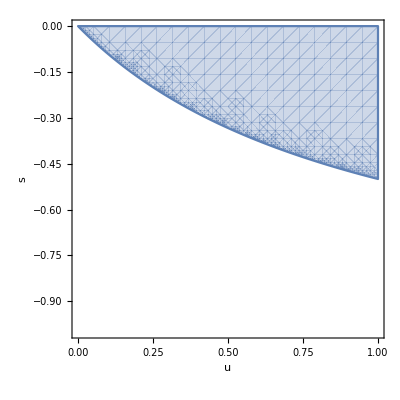

```mathematica
RegionPlot[stab1,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
jac2=jac/.sol[[2]]//Simplify
```

1+u+u^2+s (1+u)^2

```mathematica
stab2=Reduce[{-1<jac2<1,0<u<1,-1<s<0}]
```

0<u<1&&-1<s<-u/(1+u)

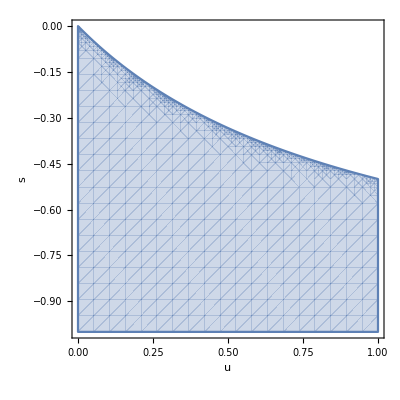

```mathematica
RegionPlot[stab2,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
k̄[1]/.sol[[2]]//Simplify
```

-u/(s+s u)

```mathematica
𝒱[1]/.sol[[2]]//Simplify
```

-(u (s+u+s u))/(s^2 (1+u)^2)

```mathematica
𝒮[1]/.sol[[2]]//Simplify
```

-(u (2 u^2+3 s u (1+u)+s^2 (1+u)^2))/(s^3 (1+u)^3)

### Diploidy (n=2)

```mathematica
nextf=f[2]+delta[2,s,u]
```

{-2 u f_0+f_0/(f_0+(1+s) (1-f_0-f_1)+(1+s/2) f_1),2 u f_0-u f_1+((1+s/2) f_1)/(f_0+(1+s) (1-f_0-f_1)+(1+s/2) f_1),u (1-f_0)+((1+s) (1-f_0-f_1))/(f_0+(1+s) (1-f_0-f_1)+(1+s/2) f_1)}

```mathematica
sol=Solve[Table[nextf[[k+1]]==Subscript[f, k],{k,0,1}],Table[Subscript[f, k],{k,0,1}]]//Simplify
```

{{f_0→0,f_1→0},{f_0→0,f_1→(s+2 u+2 s u)/(s+s u)},{f_0→(s+2 u+2 s u)^2/(s+2 s u)^2,f_1→-(4 u (s+2 u+2 s u))/(s+2 s u)^2}}

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0},{f_0→0,f_1→0.981019},{f_0→0.960478,f_1→0.0391234}}

```mathematica
sol[[3]]==eq[2,s,u]//Simplify
```

True

```mathematica
valid2=Table[{Reduce[{0≤Values[sol[[i]][[1]]]≤1,0<u<1,-1<s<0}]},{i,1,3}]
```

{{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s≤-u/(1+2 u)}}

```mathematica
jac=Table[Table[D[nextf[[i]],Subscript[f, j]],{j,0,1}],{i,1,2}]
```

{{-2 u+(4 s f_0)/(2+2 s-2 s f_0-s f_1)^2+2/(2+2 s-2 s f_0-s f_1),(2 s f_0)/(2+2 s-2 s f_0-s f_1)^2},{2 u+(2 s (2+s) f_1)/(-2 (1+s)+2 s f_0+s f_1)^2,-u+(s (2+s) f_1)/(-2 (1+s)+2 s f_0+s f_1)^2-(2+s)/(-2 (1+s)+2 s f_0+s f_1)}}

```mathematica
jac1=jac/.sol[[1]]//Simplify
```

{{1/(1+s)-2 u,0},{2 u,(2+s)/(2+2 s)-u}}

```mathematica
eig1=Eigenvalues[jac1]//Simplify
```

{(2+s-2 u-2 s u)/(2+2 s),(1-2 (1+s) u)/(1+s)}

```mathematica
stab1=Reduce[Flatten[{Table[-1<eig1[[i]]<1,{i,1,2}],0<u<1,-1<s<0}]]
```

0<u<1&&-(2 u)/(1+2 u)<s<0

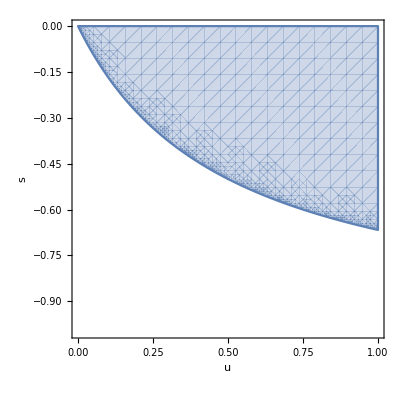

```mathematica
RegionPlot[stab1,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
jac2=jac/.sol[[2]]//Simplify
```

{{-(2 (-1+u+s u))/(2+s),0},{(2 (2 u (2+u)+s (1+4 u+2 u^2)))/(2+s),(2 (1+u+u^2)+s (2+3 u+2 u^2))/(2+s)}}

```mathematica
eig2=Eigenvalues[jac2]//Simplify
```

{-(2 (-1+u+s u))/(2+s),(2 (1+u+u^2)+s (2+3 u+2 u^2))/(2+s)}

```mathematica
stab2=Reduce[Flatten[{Table[-1<eig2[[i]]<1,{i,1,2}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac3=jac/.sol[[3]]//Simplify
```

{{((1+s) (4 u^2+s (1+2 u)^2))/s,(s+2 u+2 s u)^2/(2 s)},{-(2 (1+s) u (s+4 u+2 s u))/s,1-u-6 u^2-(4 u^2)/s+s (1/2-2 u^2)}}

```mathematica
eig3=Eigenvalues[jac3]//Simplify
```

{(1+s) (1+2 u),1+u+2 u^2+1/2 s (1+2 u)^2}

```mathematica
stab3=Reduce[Flatten[{Table[-1<eig3[[i]]<1,{i,1,2}],0<u<1,-1<s<0}]]
```

0<u<1&&-1<s<-(2 u)/(1+2 u)

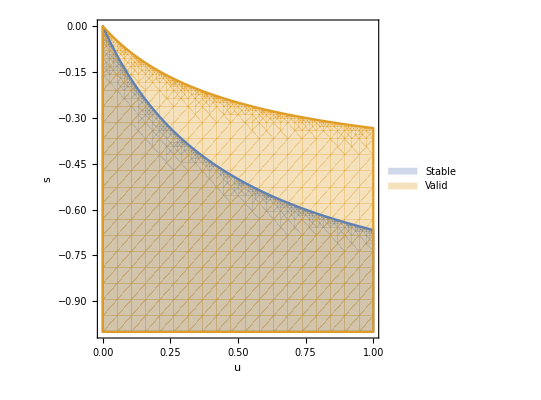

```mathematica
RegionPlot[{stab3,valid2[[3]]},{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5,PlotLegends->{ "Stable","Valid"}]
```

```mathematica
k̄[2]/.sol[[3]]//Simplify
```

-(4 u)/(s+2 s u)

```mathematica
𝒱[2]/.sol[[3]]//Simplify
```

-(4 u (s+2 u+2 s u))/(s+2 s u)^2

```mathematica
𝒮[2]/.sol[[3]]//Simplify
```

-(4 u (8 u^2+6 s u (1+2 u)+(s+2 s u)^2))/(s+2 s u)^3

### Triploidy (n=3)

```mathematica
nextf=f[3]+delta[3,s,u];
```

```mathematica
sol=Solve[Table[nextf[[k+1]]==Subscript[f, k],{k,0,2}],Table[Subscript[f, k],{k,0,2}]]//Simplify
```

{{f_0→0,f_1→0,f_2→0},{f_0→0,f_1→0,f_2→(s+3 u+3 s u)/(s+s u)},{f_0→0,f_1→(s+3 u+3 s u)^2/(s+2 s u)^2,f_2→-(2 (3+s) u (s+3 u+3 s u))/(s+2 s u)^2},{f_0→(s+3 u+3 s u)^3/(s+3 s u)^3,f_1→-(9 u (s+3 u+3 s u)^2)/(s+3 s u)^3,f_2→(27 u^2 (s+3 u+3 s u))/(s+3 s u)^3}}

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0,f_2→0},{f_0→0,f_1→0,f_2→0.972028},{f_0→0,f_1→0.942953,f_2→0.0562089},{f_0→0.912926,f_1→0.0844433,f_2→0.0026036}}

```mathematica
sol[[4]]==eq[3,s,u]//Simplify
```

True

```mathematica
valid3=Table[{Reduce[{0≤Values[sol[[i]][[1]]]≤1,0<u<1,-1<s<0}]},{i,1,4}]
```

{{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s≤-(3 u)/(1+3 u)}}

```mathematica
jac=Table[Table[D[nextf[[i]],Subscript[f, j]],{j,0,2}],{i,1,3}]
```

{{-(9 s u f_0)/(-3-3 s+3 s f_0+2 s f_1+s f_2)+(9 s f_0 (1-3 u-3 s u+3 s u f_0+2 s u f_1+s u f_2))/(-3-3 s+3 s f_0+2 s f_1+s f_2)^2-(3 (1-3 u-3 s u+3 s u f_0+2 s u f_1+s u f_2))/(-3-3 s+3 s f_0+2 s f_1+s f_2),-(6 s u f_0)/(-3-3 s+3 s f_0+2 s f_1+s f_2)+(6 s f_0 (1-3 u-3 s u+3 s u f_0+2 s u f_1+s u f_2))/(-3-3 s+3 s f_0+2 s f_1+s f_2)^2,-(3 s u f_0)/(-3-3 s+3 s f_0+2 s f_1+s f_2)+(3 s f_0 (1-3 u-3 s u+3 s u f_0+2 s u f_1+s u f_2))/(-3-3 s+3 s f_0+2 s f_1+s f_2)^2},{3 u+(3 s (3+s) f_1)/(-3-3 s+3 s f_0+2 s f_1+s f_2)^2,-2 u+(2 s (3+s) f_1)/(-3-3 s+3 s f_0+2 s f_1+s f_2)^2-(3+s)/(-3-3 s+3 s f_0+2 s f_1+s f_2),(s (3+s) f_1)/(-3-3 s+3 s f_0+2 s f_1+s f_2)^2},{(3 s (3+2 s) f_2)/(-3-3 s+3 s f_0+2 s f_1+s f_2)^2,2 u+(2 s (3+2 s) f_2)/(-3-3 s+3 s f_0+2 s f_1+s f_2)^2,-u+(s (3+2 s) f_2)/(-3-3 s+3 s f_0+2 s f_1+s f_2)^2-(3+2 s)/(-3-3 s+3 s f_0+2 s f_1+s f_2)}}

```mathematica
jac1=jac/.sol[[1]]//Simplify
```

{{(1-3 (1+s) u)/(1+s),0,0},{3 u,(3+s)/(3+3 s)-2 u,0},{0,2 u,(3+2 s)/(3+3 s)-u}}

```mathematica
eig1=Eigenvalues[jac1]//Simplify
```

{(3+s-6 u-6 s u)/(3+3 s),(3+2 s-3 u-3 s u)/(3+3 s),(1-3 (1+s) u)/(1+s)}

```mathematica
stab1=Reduce[Flatten[{Table[-1<eig1[[i]]<1,{i,1,3}],0<u<1,-1<s<0}]]
```

(0<u≤2/3&&-(3 u)/(1+3 u)<s<0)||(2/3<u<1&&-(3 u)/(1+3 u)<s<(2-3 u)/(-1+3 u))

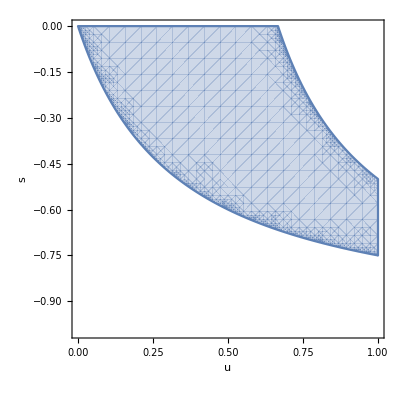

```mathematica
RegionPlot[stab1,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
jac2=jac/.sol[[2]]//Simplify
```

{{(3-6 (1+s) u)/(3+2 s),0,0},{3 u,(3+s-3 u-3 s u)/(3+2 s),0},{(3 (1+u) (s+3 u+3 s u))/(3+2 s),(2 (3 u (2+u)+s (1+6 u+3 u^2)))/(3+2 s),(3 (1+u+u^2)+s (3+4 u+3 u^2))/(3+2 s)}}

```mathematica
eig2=Eigenvalues[jac2]//Simplify
```

{(3+s-3 u-3 s u)/(3+2 s),(3-6 (1+s) u)/(3+2 s),(3 (1+u+u^2)+s (3+4 u+3 u^2))/(3+2 s)}

```mathematica
stab2=Reduce[Flatten[{Table[-1<eig2[[i]]<1,{i,1,3}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac3=jac/.sol[[3]]//Simplify
```

{{-(3 (-1+u+s u))/(3+s),0,0},{(3 (9 u^2+9 s u (1+2 u)+s^2 (1+7 u+9 u^2)))/(s (3+s)),(3 (1+s) (s+4 s u+6 u^2+6 s u^2))/(s (3+s)),(s+3 u+3 s u)^2/(s (3+s))},{-(6 (3+2 s) u (s+3 u+3 s u))/(s (3+s)),-(6 (1+s) u (s+6 u+4 s u))/(s (3+s)),-(18 u^2+3 s (-1+u+10 u^2)+s^2 (-2+u+12 u^2))/(s (3+s))}}

```mathematica
eig3=Eigenvalues[jac3]//Simplify
```

{-(3 (-1+u+s u))/(3+s),(3 (1+s) (1+2 u))/(3+s),(3+2 s+3 u+5 s u+6 u^2+6 s u^2)/(3+s)}

```mathematica
stab3=Reduce[Flatten[{Table[-1<eig3[[i]]<1,{i,1,3}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac4=jac/.sol[[4]]//Simplify
```

{{(27 u^3+27 s u^2 (1+3 u)+(s+3 s u)^3+s^2 (1+12 u+54 u^2+81 u^3))/(s^2 (1+3 u)),(2 (s+3 u+3 s u)^3)/(3 s^2 (1+3 u)),(s+3 u+3 s u)^3/(3 s^2 (1+3 u))},{-(3 u (27 u^2+s^3 (1+3 u)^2+9 s u (2+7 u)+s^2 (2+21 u+45 u^2)))/(s^2 (1+3 u)),-(162 u^3+s^3 (1+3 u)^2 (-1+6 u)+54 s u^2 (2+7 u)+3 s^2 (-1+2 u+45 u^2+90 u^3))/(3 s^2 (1+3 u)),-((3+s) u (s+3 u+3 s u)^2)/(s^2 (1+3 u))},{(9 (3+2 s) u^2 (s+3 u+3 s u))/(s^2 (1+3 u)),(2 u (27 u^2+9 s u (1+5 u)+s^2 (1+9 u+18 u^2)))/(s^2 (1+3 u)),(81 u^3+2 s^3 (1+3 u)^2+27 s u^2 (1+5 u)+3 s^2 (1+5 u+12 u^2+18 u^3))/(3 s^2 (1+3 u))}}

```mathematica
eig4=Eigenvalues[jac4]//Simplify
```

{(1+s) (1+3 u),1+u+3 u^2+1/3 s (1+3 u)^2,1+2 u+s (2/3+2 u)}

```mathematica
stab4=Reduce[Flatten[{Table[-1<eig4[[i]]<1,{i,1,3}],0<u<1,-1<s<0}]]
```

0<u<1&&-1<s<-(3 u)/(1+3 u)

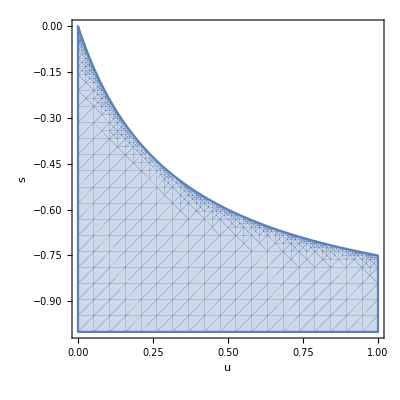

```mathematica
RegionPlot[stab4,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
k̄[3]/.sol[[4]]//Simplify
```

-(9 u)/(s+3 s u)

```mathematica
𝒱[3]/.sol[[4]]//Simplify
```

-(9 u (s+3 u+3 s u))/(s+3 s u)^2

```mathematica
𝒮[3]/.sol[[4]]//Simplify
```

-(9 u (18 u^2+9 s u (1+3 u)+(s+3 s u)^2))/(s+3 s u)^3

### Tetraploidy (n=4)

```mathematica
nextf=f[4]+delta[4,s,u];
```

```mathematica
sol=Solve[Table[nextf[[k+1]]==Subscript[f, k],{k,0,3}],Table[Subscript[f, k],{k,0,3}]]//Simplify
```

{{f_0→0,f_1→0,f_2→0,f_3→0},{f_0→0,f_1→0,f_2→0,f_3→(s+4 u+4 s u)/(s+s u)},{f_0→0,f_1→0,f_2→(s+4 u+4 s u)^2/(s+2 s u)^2,f_3→-(4 (2+s) u (s+4 u+4 s u))/(s+2 s u)^2},{f_0→0,f_1→(s+4 u+4 s u)^3/(s+3 s u)^3,f_2→-(3 (4+s) u (s+4 u+4 s u)^2)/(s+3 s u)^3,f_3→(3 (4+s)^2 u^2 (s+4 u+4 s u))/(s+3 s u)^3},{f_0→(s+4 u+4 s u)^4/(s+4 s u)^4,f_1→-(16 u (s+4 u+4 s u)^3)/(s+4 s u)^4,f_2→(96 u^2 (s+4 u+4 s u)^2)/(s+4 s u)^4,f_3→-(256 u^3 (s+4 u+4 s u))/(s+4 s u)^4}}

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0,f_2→0,f_3→0},{f_0→0,f_1→0,f_2→0,f_3→0.963037},{f_0→0,f_1→0,f_2→0.92559,f_3→0.0729718},{f_0→0,f_1→0.887827,f_2→0.107755,f_3→0.00435938},{f_0→0.849911,f_1→0.141064,f_2→0.00877992,f_3→0.000242875}}

```mathematica
sol[[5]]==eq[4,s,u]//Simplify
```

True

```mathematica
valid4=Table[{Reduce[{0≤Values[sol[[i]][[1]]]≤1,0<u<1,-1<s<0}]},{i,1,5}]
```

{{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s≤-(2 u)/(1+4 u)}}

```mathematica
jac=Table[Table[D[nextf[[i]],Subscript[f, j]],{j,0,3}],{i,1,4}]
```

{{-(16 s u f_0)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)+(16 s f_0 (1-4 u-4 s u+4 s u f_0+3 s u f_1+2 s u f_2+s u f_3))/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2-(4 (1-4 u-4 s u+4 s u f_0+3 s u f_1+2 s u f_2+s u f_3))/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3),-(12 s u f_0)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)+(12 s f_0 (1-4 u-4 s u+4 s u f_0+3 s u f_1+2 s u f_2+s u f_3))/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2,-(8 s u f_0)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)+(8 s f_0 (1-4 u-4 s u+4 s u f_0+3 s u f_1+2 s u f_2+s u f_3))/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2,-(4 s u f_0)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)+(4 s f_0 (1-4 u-4 s u+4 s u f_0+3 s u f_1+2 s u f_2+s u f_3))/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2},{4 u+(4 s (4+s) f_1)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2,-3 u+(3 s (4+s) f_1)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2-(4+s)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3),(2 s (4+s) f_1)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2,(s (4+s) f_1)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2},{(8 s (2+s) f_2)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2,3 u+(6 s (2+s) f_2)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2,-2 u+(4 s (2+s) f_2)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2-(2 (2+s))/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3),(2 s (2+s) f_2)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2},{(4 s (4+3 s) f_3)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2,(3 s (4+3 s) f_3)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2,2 u+(2 s (4+3 s) f_3)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2,-u+(s (4+3 s) f_3)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)^2-(4+3 s)/(-4-4 s+4 s f_0+3 s f_1+2 s f_2+s f_3)}}

```mathematica
jac1=jac/.sol[[1]]//Simplify
```

{{(1-4 (1+s) u)/(1+s),0,0,0},{4 u,(4+s)/(4+4 s)-3 u,0,0},{0,3 u,(2+s)/(2+2 s)-2 u,0},{0,0,2 u,(4+3 s)/(4+4 s)-u}}

```mathematica
eig1=Eigenvalues[jac1]//Simplify
```

{(4+s-12 u-12 s u)/(4+4 s),(4+3 s-4 u-4 s u)/(4+4 s),(1-4 (1+s) u)/(1+s),(2+s-4 u-4 s u)/(2+2 s)}

```mathematica
stab1=Reduce[Flatten[{Table[-1<eig1[[i]]<1,{i,1,4}],0<u<1,-1<s<0}]]
```

(0<u≤1/2&&-(4 u)/(1+4 u)<s<0)||(1/2<u<1&&-(4 u)/(1+4 u)<s<(2-4 u)/(-1+4 u))

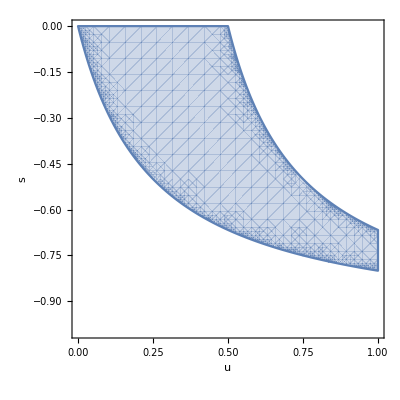

```mathematica
RegionPlot[stab1,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
jac2=jac/.sol[[2]]//Simplify
```

{{-(4 (-1+3 (1+s) u))/(4+3 s),0,0,0},{4 u,(4+s-8 u-8 s u)/(4+3 s),0,0},{0,3 u,(4+2 s-4 u-4 s u)/(4+3 s),0},{(4 (1+u) (s+4 u+4 s u))/(4+3 s),(3 (1+u) (s+4 u+4 s u))/(4+3 s),(2 (4 u (2+u)+s (1+8 u+4 u^2)))/(4+3 s),(4 (1+u+u^2)+s (4+5 u+4 u^2))/(4+3 s)}}

```mathematica
eig2=Eigenvalues[jac2]//Simplify
```

{(4+s-8 u-8 s u)/(4+3 s),(4+2 s-4 u-4 s u)/(4+3 s),-(4 (-1+3 (1+s) u))/(4+3 s),(4 (1+u+u^2)+s (4+5 u+4 u^2))/(4+3 s)}

```mathematica
stab2=Reduce[Flatten[{Table[-1<eig2[[i]]<1,{i,1,4}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac3=jac/.sol[[3]]//Simplify
```

{{(2-4 (1+s) u)/(2+s),0,0,0},{4 u,(4+s-4 u-4 s u)/(4+2 s),0,0},{(2 (s+4 u+4 s u)^2)/(s (2+s)),(3 (16 u^2+4 s u (3+8 u)+s^2 (1+10 u+16 u^2)))/(2 s (2+s)),(2 (1+s) (s+4 s u+8 u^2+8 s u^2))/(s (2+s)),(s+4 u+4 s u)^2/(2 s (2+s))},{-(4 (4+3 s) u (s+4 u+4 s u))/(s (2+s)),-(3 (4+3 s) u (s+4 u+4 s u))/(s (2+s)),-(4 (1+s) u (s+8 u+6 s u))/(s (2+s)),(-32 u^2+s^2 (3-2 u-24 u^2)-4 s (-1+u+14 u^2))/(2 s (2+s))}}

```mathematica
eig3=Eigenvalues[jac3]//Simplify
```

{(2-4 (1+s) u)/(2+s),(4+s-4 u-4 s u)/(4+2 s),(2 (1+s) (1+2 u))/(2+s),(4+3 s+4 u+6 s u+8 u^2+8 s u^2)/(4+2 s)}

```mathematica
stab3=Reduce[Flatten[{Table[-1<eig3[[i]]<1,{i,1,4}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac4=jac/.sol[[4]]//Simplify
```

{{-(4 (-1+u+s u))/(4+s),0,0,0},{(4 (64 u^3+48 s u^2 (1+4 u)+4 s^2 u (4+27 u+48 u^2)+s^3 (1+13 u+51 u^2+64 u^3)))/(s^2 (4+s) (1+3 u)),(192 u^3+144 s u^2 (1+4 u)+4 s^2 (1+12 u+72 u^2+144 u^3)+s^3 (4+39 u+144 u^2+192 u^3))/(s^2 (4+s) (1+3 u)),(2 (s+4 u+4 s u)^3)/(s^2 (4+s) (1+3 u)),(s+4 u+4 s u)^3/(s^2 (4+s) (1+3 u))},{-(24 (2+s) u (s+4 u+4 s u)^2)/(s^2 (4+s) (1+3 u)),-(3 u (192 u^2+96 s u (1+5 u)+4 s^2 (2+33 u+96 u^2)+s^3 (5+45 u+96 u^2)))/(s^2 (4+s) (1+3 u)),-1/(s^2 (4+s) (1+3 u))2 (192 u^3+96 s u^2 (1+5 u)+s^3 (-1+u+42 u^2+96 u^3)+2 s^2 (-1+2 u+69 u^2+192 u^3)),-(6 (2+s) u (s+4 u+4 s u)^2)/(s^2 (4+s) (1+3 u))},{(12 (4+3 s) u^2 (s+4 u+4 s u))/(s^2 (1+3 u)),(9 (4+3 s) u^2 (s+4 u+4 s u))/(s^2 (1+3 u)),(2 u (48 u^2+12 s u (1+7 u)+(s+6 s u)^2))/(s^2 (1+3 u)),(192 u^3+48 s u^2 (1+8 u)+s^3 (3+17 u+33 u^2+36 u^3)+4 s^2 (1+5 u+18 u^2+57 u^3))/(s^2 (4+s) (1+3 u))}}

```mathematica
eig4=Eigenvalues[jac4]//Simplify
```

{(4 (1+s) (1+3 u))/(4+s),-(4 (-1+u+s u))/(4+s),(4 (1+u+3 u^2)+s (2+7 u+12 u^2))/(4+s),(4+3 s+8 u+8 s u)/(4+s)}

```mathematica
stab4=Reduce[Flatten[{Table[-1<eig4[[i]]<1,{i,1,4}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac5=jac/.sol[[5]]//Simplify
```

{{(256 u^4+256 s u^3 (1+4 u)+96 s^2 u^2 (1+4 u)^2+(s+4 s u)^4+s^3 (1+12 u+32 u^2)^2)/(s^3 (1+4 u)^2),(3 (s+4 u+4 s u)^4)/(4 s^3 (1+4 u)^2),(s+4 u+4 s u)^4/(2 s^3 (1+4 u)^2),(s+4 u+4 s u)^4/(4 s^3 (1+4 u)^2)},{-1/(s^3 (1+4 u)^2)4 u (256 u^3+s^4 (1+4 u)^3+64 s u^2 (3+13 u)+s^3 (1+4 u)^2 (3+28 u)+48 s^2 u (1+9 u+20 u^2)),-1/(4 s^3 (1+4 u)^2)(3072 u^4+s^4 (1+4 u)^3 (-1+12 u)+768 s u^3 (3+13 u)+576 s^2 u^2 (1+9 u+20 u^2)+4 s^3 (1+4 u)^2 (-1+11 u+84 u^2)),-(2 (4+s) u (s+4 u+4 s u)^3)/(s^3 (1+4 u)^2),-((4+s) u (s+4 u+4 s u)^3)/(s^3 (1+4 u)^2)},{(48 (2+s) u^2 (s+4 u+4 s u)^2)/(s^3 (1+4 u)^2),(3 u (384 u^3+192 s u^2 (1+5 u)+s^3 (1+4 u)^2 (1+12 u)+24 s^2 u (1+12 u+32 u^2)))/(s^3 (1+4 u)^2),1/(2 s^3 (1+4 u)^2)(1536 u^4+s^4 (1+4 u)^3+768 s u^3 (1+5 u)+2 s^3 (1+4 u)^2 (1+2 u+24 u^2)+96 s^2 u^2 (1+12 u+32 u^2)),(12 (2+s) u^2 (s+4 u+4 s u)^2)/(s^3 (1+4 u)^2)},{-(64 (4+3 s) u^3 (s+4 u+4 s u))/(s^3 (1+4 u)^2),-(48 (4+3 s) u^3 (s+4 u+4 s u))/(s^3 (1+4 u)^2),(2 u (-256 u^3-48 s^2 u^2 (1+4 u)+s^3 (1+4 u)^2-64 s u^2 (1+7 u)))/(s^3 (1+4 u)^2),1/(4 s^3 (1+4 u)^2)(-1024 u^4-192 s^2 u^3 (1+4 u)+4 s^3 (1+3 u) (1+4 u)^2+3 s^4 (1+4 u)^3-256 s u^3 (1+7 u))}}

```mathematica
eig5=Eigenvalues[jac5]//Simplify
```

{(1+s) (1+4 u),1/2 (2+s+4 u+4 s u),1+3 u+s (3/4+3 u),1+u+4 u^2+1/4 s (1+4 u)^2}

```mathematica
stab5=Reduce[Flatten[{Table[-1<eig5[[i]]<1,{i,1,4}],0<u<1,-1<s<0}]]
```

0<u<1&&-1<s<-(4 u)/(1+4 u)

```mathematica
valid5=Reduce[Flatten[{Table[0<Values[sol[[5]]][[i]]<1,{i,1,4}],0<u<1,-1<s<0}]]
```

0<u<1&&-1<s<-(4 u)/(1+4 u)

```mathematica
stab5==valid5
```

True

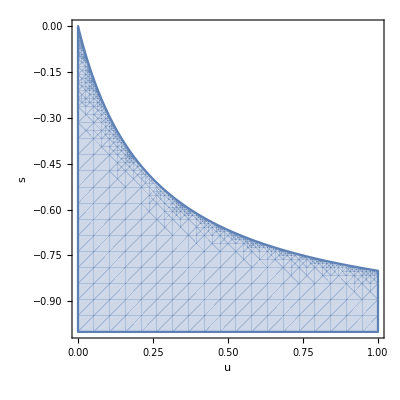

```mathematica
RegionPlot[stab5,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
k̄[4]/.sol[[5]]//Simplify
```

-(16 u)/(s+4 s u)

```mathematica
𝒱[4]/.sol[[5]]//Simplify
```

-(16 u (s+4 u+4 s u))/(s+4 s u)^2

```mathematica
𝒮[4]/.sol[[5]]//Simplify
```

-(16 u (32 u^2+12 s u (1+4 u)+(s+4 s u)^2))/(s+4 s u)^3

### n=5

```mathematica
nextf=f[5]+delta[5,s,u];
```

```mathematica
sol=Solve[Table[nextf[[k+1]]==Subscript[f, k],{k,0,4}],Table[Subscript[f, k],{k,0,4}]]//Simplify
```

{{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→(s+5 u+5 s u)/(s+s u)},{f_0→0,f_1→0,f_2→0,f_3→(s+5 u+5 s u)^2/(s+2 s u)^2,f_4→-(2 (5+3 s) u (s+5 u+5 s u))/(s+2 s u)^2},{f_0→0,f_1→0,f_2→(s+5 u+5 s u)^3/(s+3 s u)^3,f_3→-(3 (5+2 s) u (s+5 u+5 s u)^2)/(s+3 s u)^3,f_4→(3 (5+2 s)^2 u^2 (s+5 u+5 s u))/(s+3 s u)^3},{f_0→0,f_1→(s+5 u+5 s u)^4/(s+4 s u)^4,f_2→-(4 (5+s) u (s+5 u+5 s u)^3)/(s+4 s u)^4,f_3→(6 (5+s)^2 u^2 (s+5 u+5 s u)^2)/(s+4 s u)^4,f_4→-(4 (5+s)^3 u^3 (s+5 u+5 s u))/(s+4 s u)^4},{f_0→(s+5 u+5 s u)^5/(s+5 s u)^5,f_1→-(25 u (s+5 u+5 s u)^4)/(s+5 s u)^5,f_2→(250 u^2 (s+5 u+5 s u)^3)/(s+5 s u)^5,f_3→-(1250 u^3 (s+5 u+5 s u)^2)/(s+5 s u)^5,f_4→(3125 u^4 (s+5 u+5 s u))/(s+5 s u)^5}}

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0.954046},{f_0→0,f_1→0,f_2→0,f_3→0.908388,f_4→0.089412},{f_0→0,f_1→0,f_2→0.863192,f_3→0.130157,f_4→0.00654191},{f_0→0,f_1→0.818613,f_2→0.168009,f_3→0.0129305,f_4→0.0004423},{f_0→0.774795,f_1→0.202826,f_2→0.0212383,f_3→0.00111195,f_4→0.0000291087}}

```mathematica
sol[[6]]==eq[5,s,u]//Simplify
```

True

```mathematica
valid5=Table[{Reduce[{0≤Values[sol[[i]][[1]]]≤1,0<u<1,-1<s<0}]},{i,1,6}]
```

{{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s≤-(5 u)/(1+5 u)}}

```mathematica
jac=Table[Table[D[nextf[[i]],Subscript[f, j]],{j,0,4}],{i,1,5}]//Simplify
```

{{-((5 (25 s^2 u f_0^2+10 s u f_0 (-5-5 s+4 s f_1+3 s f_2+2 s f_3+s f_4)+(-5-5 s+4 s f_1+3 s f_2+2 s f_3+s f_4) (1-5 u-5 s u+4 s u f_1+3 s u f_2+2 s u f_3+s u f_4)))/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2),(20 s f_0)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2,(15 s f_0)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2,(10 s f_0)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2,(5 s f_0)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2},{5 (u+(s (5+s) f_1)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2),-4 u+(4 s (5+s) f_1)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2-(5+s)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4),(3 s (5+s) f_1)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2,(2 s (5+s) f_1)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2,(s (5+s) f_1)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2},{(5 s (5+2 s) f_2)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2,4 (u+(s (5+2 s) f_2)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2),-3 u+(3 s (5+2 s) f_2)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2+(-5-2 s)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4),(2 s (5+2 s) f_2)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2,(s (5+2 s) f_2)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2},{(5 s (5+3 s) f_3)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2,(4 s (5+3 s) f_3)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2,3 (u+(s (5+3 s) f_3)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2),-2 u+(2 s (5+3 s) f_3)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2+(-5-3 s)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4),(s (5+3 s) f_3)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2},{(5 s (5+4 s) f_4)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2,(4 s (5+4 s) f_4)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2,(3 s (5+4 s) f_4)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2,2 (u+(s (5+4 s) f_4)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2),-u+(s (5+4 s) f_4)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)^2+(-5-4 s)/(-5-5 s+5 s f_0+4 s f_1+3 s f_2+2 s f_3+s f_4)}}

```mathematica
jac1=jac/.sol[[1]]//Simplify
```

{{(1-5 (1+s) u)/(1+s),0,0,0,0},{5 u,(5+s)/(5+5 s)-4 u,0,0,0},{0,4 u,(5+2 s)/(5+5 s)-3 u,0,0},{0,0,3 u,(5+3 s)/(5+5 s)-2 u,0},{0,0,0,2 u,(5+4 s)/(5+5 s)-u}}

```mathematica
eig1=Eigenvalues[jac1]//Simplify
```

{(5+s-20 u-20 s u)/(5+5 s),(5+2 s-15 u-15 s u)/(5+5 s),(5+3 s-10 u-10 s u)/(5+5 s),(5+4 s-5 u-5 s u)/(5+5 s),(1-5 (1+s) u)/(1+s)}

```mathematica
stab1=Reduce[Flatten[{Table[-1<eig1[[i]]<1,{i,1,5}],0<u<1,-1<s<0}]]
```

(0<u≤2/5&&-(5 u)/(1+5 u)<s<0)||(2/5<u<1&&-(5 u)/(1+5 u)<s<(2-5 u)/(-1+5 u))

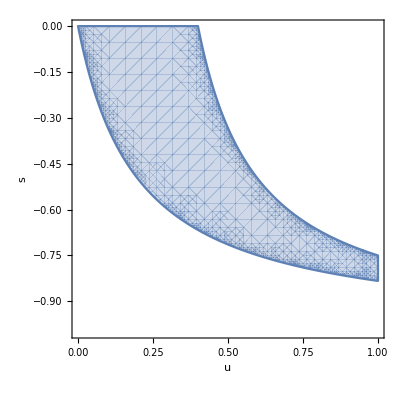

```mathematica
RegionPlot[stab1,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
jac2=jac/.sol[[2]]//Simplify
```

{{-(5 (-1+4 (1+s) u))/(5+4 s),0,0,0,0},{5 u,(5+s-15 u-15 s u)/(5+4 s),0,0,0},{0,4 u,(5+2 s-10 u-10 s u)/(5+4 s),0,0},{0,0,3 u,(5+3 s-5 u-5 s u)/(5+4 s),0},{(5 (1+u) (s+5 u+5 s u))/(5+4 s),(4 (1+u) (s+5 u+5 s u))/(5+4 s),(3 (1+u) (s+5 u+5 s u))/(5+4 s),(2 (5 u (2+u)+s (1+10 u+5 u^2)))/(5+4 s),(5 (1+u+u^2)+s (5+6 u+5 u^2))/(5+4 s)}}

```mathematica
eig2=Eigenvalues[jac2]//Simplify
```

{(5+s-15 u-15 s u)/(5+4 s),(5+2 s-10 u-10 s u)/(5+4 s),(5+3 s-5 u-5 s u)/(5+4 s),-(5 (-1+4 (1+s) u))/(5+4 s),(5 (1+u+u^2)+s (5+6 u+5 u^2))/(5+4 s)}

```mathematica
stab2=Reduce[Flatten[{Table[-1<eig2[[i]]<1,{i,1,5}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac3=jac/.sol[[3]]//Simplify
```

{{-(5 (-1+3 (1+s) u))/(5+3 s),0,0,0,0},{5 u,(5+s-10 u-10 s u)/(5+3 s),0,0,0},{0,4 u,(5+2 s-5 u-5 s u)/(5+3 s),0,0},{(5 (s+5 u+5 s u)^2)/(s (5+3 s)),(4 (s+5 u+5 s u)^2)/(s (5+3 s)),(3 (25 u^2+5 s u (3+10 u)+s^2 (1+13 u+25 u^2)))/(s (5+3 s)),(5 (1+s) (s+4 s u+10 u^2+10 s u^2))/(s (5+3 s)),(s+5 u+5 s u)^2/(s (5+3 s))},{-(10 (5+4 s) u (s+5 u+5 s u))/(s (5+3 s)),-(8 (5+4 s) u (s+5 u+5 s u))/(s (5+3 s)),-(6 (5+4 s) u (s+5 u+5 s u))/(s (5+3 s)),-(10 (1+s) u (s+10 u+8 s u))/(s (5+3 s)),(-50 u^2+s^2 (4-3 u-40 u^2)-5 s (-1+u+18 u^2))/(s (5+3 s))}}

```mathematica
eig3=Eigenvalues[jac3]//Simplify
```

{-(5 (-1+3 (1+s) u))/(5+3 s),(5+2 s-5 u-5 s u)/(5+3 s),(5+s-10 u-10 s u)/(5+3 s),(5 (1+s) (1+2 u))/(5+3 s),(5 (1+u+2 u^2)+s (4+7 u+10 u^2))/(5+3 s)}

```mathematica
stab3=Reduce[Flatten[{Table[-1<eig3[[i]]<1,{i,1,5}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac4=jac/.sol[[4]]//Simplify
```

{{-(5 (-1+2 (1+s) u))/(5+2 s),0,0,0,0},{5 u,(5+s-5 u-5 s u)/(5+2 s),0,0,0},{(5 (s+5 u+5 s u)^3)/(s^2 (5+2 s) (1+3 u)),(4 (125 u^3+75 s u^2 (1+5 u)+5 s^2 u (4+33 u+75 u^2)+s^3 (1+17 u+81 u^2+125 u^3)))/(s^2 (5+2 s) (1+3 u)),(375 u^3+225 s u^2 (1+5 u)+5 s^2 (1+12 u+90 u^2+225 u^3)+s^3 (5+51 u+225 u^2+375 u^3))/(s^2 (5+2 s) (1+3 u)),(2 (s+5 u+5 s u)^3)/(s^2 (5+2 s) (1+3 u)),(s+5 u+5 s u)^3/(s^2 (5+2 s) (1+3 u))},{-(15 (5+3 s) u (s+5 u+5 s u)^2)/(s^2 (5+2 s) (1+3 u)),-(12 (5+3 s) u (s+5 u+5 s u)^2)/(s^2 (5+2 s) (1+3 u)),-(3 u (375 u^2+75 s u (2+13 u)+5 s^2 (2+45 u+165 u^2)+s^3 (7+84 u+225 u^2)))/(s^2 (5+2 s) (1+3 u)),-1/(s^2 (5+2 s) (1+3 u))(750 u^3+150 s u^2 (2+13 u)+5 s^2 (-1+2 u+93 u^2+330 u^3)+s^3 (-3+4 u+165 u^2+450 u^3)),-(3 (5+3 s) u (s+5 u+5 s u)^2)/(s^2 (5+2 s) (1+3 u))},{(15 (5+4 s) u^2 (s+5 u+5 s u))/(s^2 (1+3 u)),(12 (5+4 s) u^2 (s+5 u+5 s u))/(s^2 (1+3 u)),(9 (5+4 s) u^2 (s+5 u+5 s u))/(s^2 (1+3 u)),(2 u (75 u^2+15 s u (1+9 u)+s^2 (1+15 u+60 u^2)))/(s^2 (1+3 u)),(375 u^3+75 s u^2 (1+11 u)+2 s^3 (2+11 u+27 u^2+60 u^3)+5 s^2 (1+5 u+24 u^2+114 u^3))/(s^2 (5+2 s) (1+3 u))}}

```mathematica
eig4=Eigenvalues[jac4]//Simplify
```

{(5 (1+s) (1+3 u))/(5+2 s),-(5 (-1+2 (1+s) u))/(5+2 s),(5+s-5 u-5 s u)/(5+2 s),(5 (1+u+3 u^2)+s (3+8 u+15 u^2))/(5+2 s),(5+4 s+10 u+10 s u)/(5+2 s)}

```mathematica
stab4=Reduce[Flatten[{Table[-1<eig4[[i]]<1,{i,1,5}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac5=jac/.sol[[5]]//Simplify
```

{{-(5 (-1+u+s u))/(5+s),0,0,0,0},{1/(s^3 (5+s) (1+4 u)^2)5 (625 u^4+500 s u^3 (1+5 u)+150 s^2 u^2 (1+5 u)^2+5 s^3 u (5+68 u+316 u^2+500 u^3)+s^4 (1+21 u+158 u^2+516 u^3+625 u^4)),1/(s^3 (5+s) (1+4 u)^2)(2500 u^4+2000 s u^3 (1+5 u)+600 s^2 u^2 (1+5 u)^2+5 s^3 (1+24 u+256 u^2+1200 u^3+2000 u^4)+s^4 (5+88 u+616 u^2+2000 u^3+2500 u^4)),(3 (s+5 u+5 s u)^4)/(s^3 (5+s) (1+4 u)^2),(2 (s+5 u+5 s u)^4)/(s^3 (5+s) (1+4 u)^2),(s+5 u+5 s u)^4/(s^3 (5+s) (1+4 u)^2)},{-(20 (5+2 s) u (s+5 u+5 s u)^3)/(s^3 (5+s) (1+4 u)^2),-1/(s^3 (5+s) (1+4 u)^2)4 u (2500 u^3+500 s u^2 (3+17 u)+300 s^2 u (1+12 u+35 u^2)+s^4 (7+112 u+584 u^2+1000 u^3)+5 s^3 (3+76 u+524 u^2+1100 u^3)),-1/(s^3 (5+s) (1+4 u)^2)(7500 u^4+1500 s u^3 (3+17 u)+900 s^2 u^2 (1+12 u+35 u^2)+s^4 (-2+3 u+288 u^2+1720 u^3+3000 u^4)+5 s^3 (-1+3 u+228 u^2+1604 u^3+3300 u^4)),-(8 (5+2 s) u (s+5 u+5 s u)^3)/(s^3 (5+s) (1+4 u)^2),-(4 (5+2 s) u (s+5 u+5 s u)^3)/(s^3 (5+s) (1+4 u)^2)},{(30 (5+3 s) u^2 (s+5 u+5 s u)^2)/(s^3 (1+4 u)^2),(24 (5+3 s) u^2 (s+5 u+5 s u)^2)/(s^3 (1+4 u)^2),1/(s^3 (1+4 u)^2)3 u (750 u^3+150 s u^2 (2+13 u)+30 s^2 u (1+16 u+55 u^2)+s^3 (1+26 u+196 u^2+450 u^3)),1/(s^3 (5+s) (1+4 u)^2)(7500 u^4+3000 s u^3 (1+7 u)+300 s^2 u^2 (1+18 u+68 u^2)+s^4 (3+34 u+164 u^2+520 u^3+900 u^4)+5 s^3 (1+10 u+80 u^2+584 u^3+1560 u^4)),(6 (5+3 s) u^2 (s+5 u+5 s u)^2)/(s^3 (1+4 u)^2)},{-(20 (5+s) (5+4 s) u^3 (s+5 u+5 s u))/(s^3 (1+4 u)^2),-(16 (5+s) (5+4 s) u^3 (s+5 u+5 s u))/(s^3 (1+4 u)^2),-(12 (5+s) (5+4 s) u^3 (s+5 u+5 s u))/(s^3 (1+4 u)^2),-(2 u (500 u^3+100 s u^2 (1+10 u)+20 s^2 u^2 (5+29 u)+s^3 (-1-8 u+80 u^3)))/(s^3 (1+4 u)^2),1/(s^3 (5+s) (1+4 u)^2)(-2500 u^4-500 s u^3 (1+11 u)-300 s^2 u^3 (2+13 u)+s^3 (5+55 u+200 u^2+60 u^3-980 u^4)+s^4 (4+47 u+184 u^2+224 u^3-80 u^4))}}

```mathematica
eig5=Eigenvalues[jac5]//Simplify
```

{(5 (1+s) (1+4 u))/(5+s),-(5 (-1+u+s u))/(5+s),(5+3 s+10 u+10 s u)/(5+s),(5+4 s+15 u+15 s u)/(5+s),(5 (1+u+4 u^2)+s (2+9 u+20 u^2))/(5+s)}

```mathematica
stab5=Reduce[Flatten[{Table[-1<eig5[[i]]<1,{i,1,5}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac6=jac/.sol[[6]]//Simplify
```

{{1/(s^4 (1+5 u)^3)(3125 u^5+3125 s u^4 (1+5 u)+1250 u^3 (s+5 s u)^2+250 u^2 (s+5 s u)^3+(s+5 s u)^5+s^4 (1+5 u)^3 (1+25 u+125 u^2)),(4 (s+5 u+5 s u)^5)/(5 s^4 (1+5 u)^3),(3 (s+5 u+5 s u)^5)/(5 s^4 (1+5 u)^3),(2 (s+5 u+5 s u)^5)/(5 s^4 (1+5 u)^3),(s+5 u+5 s u)^5/(5 s^4 (1+5 u)^3)},{-1/(s^4 (1+5 u)^3)5 u (3125 u^4+s^5 (1+5 u)^4+50 s^3 u (1+5 u)^2 (2+13 u)+625 s u^3 (4+21 u)+s^4 (1+5 u)^3 (4+45 u)+250 s^2 u^2 (3+32 u+85 u^2)),-1/(5 s^4 (1+5 u)^3)(62500 u^5+1000 s^3 u^2 (1+5 u)^2 (2+13 u)+s^5 (1+5 u)^4 (-1+20 u)+12500 s u^4 (4+21 u)+5000 s^2 u^3 (3+32 u+85 u^2)+5 s^4 (1+5 u)^3 (-1+19 u+180 u^2)),-(3 (5+s) u (s+5 u+5 s u)^4)/(s^4 (1+5 u)^3),-(2 (5+s) u (s+5 u+5 s u)^4)/(s^4 (1+5 u)^3),-((5+s) u (s+5 u+5 s u)^4)/(s^4 (1+5 u)^3)},{(50 (5+2 s) u^2 (s+5 u+5 s u)^3)/(s^4 (1+5 u)^3),1/(s^4 (1+5 u)^3)4 u (6250 u^4+50 s^3 u (1+5 u)^2 (1+11 u)+1250 s u^3 (3+17 u)+s^4 (1+5 u)^3 (1+20 u)+750 s^2 u^2 (1+12 u+35 u^2)),1/(5 s^4 (1+5 u)^3)(93750 u^5+2 s^5 (1+5 u)^4+750 s^3 u^2 (1+5 u)^2 (1+11 u)+18750 s u^4 (3+17 u)+11250 s^2 u^3 (1+12 u+35 u^2)+5 s^4 (1+5 u)^3 (1+2 u+60 u^2)),(20 (5+2 s) u^2 (s+5 u+5 s u)^3)/(s^4 (1+5 u)^3),(10 (5+2 s) u^2 (s+5 u+5 s u)^3)/(s^4 (1+5 u)^3)},{-(250 (5+3 s) u^3 (s+5 u+5 s u)^2)/(s^4 (1+5 u)^3),-(200 (5+3 s) u^3 (s+5 u+5 s u)^2)/(s^4 (1+5 u)^3),-1/(s^4 (1+5 u)^3)3 u (6250 u^4+150 s^3 u^2 (1+5 u)^2-s^4 (1+5 u)^3+1250 s u^3 (2+13 u)+250 s^2 u^2 (1+16 u+55 u^2)),-1/(5 s^4 (1+5 u)^3)(62500 u^5+1500 s^3 u^3 (1+5 u)^2-5 s^4 (1+3 u) (1+5 u)^3-3 s^5 (1+5 u)^4+12500 s u^4 (2+13 u)+2500 s^2 u^3 (1+16 u+55 u^2)),-(50 (5+3 s) u^3 (s+5 u+5 s u)^2)/(s^4 (1+5 u)^3)},{(625 (5+4 s) u^4 (s+5 u+5 s u))/(s^4 (1+5 u)^3),(500 (5+4 s) u^4 (s+5 u+5 s u))/(s^4 (1+5 u)^3),(375 (5+4 s) u^4 (s+5 u+5 s u))/(s^4 (1+5 u)^3),(2 u (3125 u^4+500 s^2 u^3 (1+5 u)+s^4 (1+5 u)^3+625 s u^3 (1+9 u)))/(s^4 (1+5 u)^3),1/(5 s^4 (1+5 u)^3)(15625 u^5+2500 s^2 u^4 (1+5 u)+5 s^4 (1+4 u) (1+5 u)^3+4 s^5 (1+5 u)^4+3125 s u^4 (1+9 u))}}

```mathematica
eig6=Eigenvalues[jac6]//Simplify
```

{(1+s) (1+5 u),1+2 u+s (2/5+2 u),1+3 u+s (3/5+3 u),1+4 u+s (4/5+4 u),1+u+5 u^2+1/5 s (1+5 u)^2}

```mathematica
stab6=Reduce[Flatten[{Table[-1<eig6[[i]]<1,{i,1,5}],0<u<1,-1<s<0}]]
```

0<u<1&&-1<s<-(5 u)/(1+5 u)

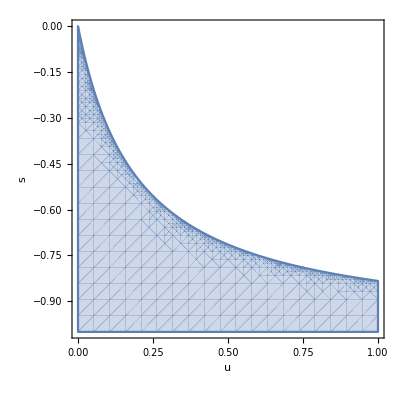

```mathematica
RegionPlot[stab6,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
k̄[5]/.sol[[6]]//Simplify
```

-(25 u)/(s+5 s u)

```mathematica
𝒱[5]/.sol[[6]]//Simplify
```

-(25 u (s+5 u+5 s u))/(s+5 s u)^2

```mathematica
𝒮[5]/.sol[[6]]//Simplify
```

-(25 u (50 u^2+15 s u (1+5 u)+(s+5 s u)^2))/(s+5 s u)^3

### n=6

```mathematica
nextf=f[6]+delta[6,s,u];
```

```mathematica
sol=Solve[Table[nextf[[k+1]]==Subscript[f, k],{k,0,5}],Table[Subscript[f, k],{k,0,5}]]//Simplify
```

{{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→(s+6 u+6 s u)/(s+s u)},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→(s+6 u+6 s u)^2/(s+2 s u)^2,f_5→-(4 (3+2 s) u (s+6 u+6 s u))/(s+2 s u)^2},{f_0→0,f_1→0,f_2→0,f_3→(s+6 u+6 s u)^3/(s+3 s u)^3,f_4→-(9 (2+s) u (s+6 u+6 s u)^2)/(s+3 s u)^3,f_5→(27 (2+s)^2 u^2 (s+6 u+6 s u))/(s+3 s u)^3},{f_0→0,f_1→0,f_2→(s+6 u+6 s u)^4/(s+4 s u)^4,f_3→-(8 (3+s) u (s+6 u+6 s u)^3)/(s+4 s u)^4,f_4→(24 (3+s)^2 u^2 (s+6 u+6 s u)^2)/(s+4 s u)^4,f_5→-(32 (3+s)^3 u^3 (s+6 u+6 s u))/(s+4 s u)^4},{f_0→0,f_1→(s+6 u+6 s u)^5/(s+5 s u)^5,f_2→-(5 (6+s) u (s+6 u+6 s u)^4)/(s+5 s u)^5,f_3→(10 (6+s)^2 u^2 (s+6 u+6 s u)^3)/(s+5 s u)^5,f_4→-(10 (6+s)^3 u^3 (s+6 u+6 s u)^2)/(s+5 s u)^5,f_5→(5 (6+s)^4 u^4 (s+6 u+6 s u))/(s+5 s u)^5},{f_0→(s+6 u+6 s u)^6/(s+6 s u)^6,f_1→-(36 u (s+6 u+6 s u)^5)/(s+6 s u)^6,f_2→(540 u^2 (s+6 u+6 s u)^4)/(s+6 s u)^6,f_3→-(4320 u^3 (s+6 u+6 s u)^3)/(s+6 s u)^6,f_4→(19440 u^4 (s+6 u+6 s u)^2)/(s+6 s u)^6,f_5→-(46656 u^5 (s+6 u+6 s u))/(s+6 s u)^6}}

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0.945055},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0.891347,f_5→0.105529},{f_0→0,f_1→0,f_2→0,f_3→0.839017,f_4→0.151662,f_5→0.00913817},{f_0→0,f_1→0,f_2→0.788188,f_3→0.193298,f_4→0.0177768,f_5→0.000726608},{f_0→0,f_1→0.738968,f_2→0.230439,f_3→0.028744,f_4→0.0017927,f_5→0.0000559035},{f_0→0.691447,f_1→0.26313,f_2→0.0417225,f_3→0.00352833,f_4→0.000167838,f_5→4.25805×10^-6}}

```mathematica
sol[[7]]==eq[6,s,u]//Simplify
```

True

```mathematica
valid6=Table[{Reduce[{0≤Values[sol[[i]][[1]]]≤1,0<u<1,-1<s<0}]},{i,1,7}]
```

{{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s≤-(3 u)/(1+6 u)}}

```mathematica
jac=Table[Table[D[nextf[[i]],Subscript[f, j]],{j,0,5}],{i,1,6}]//Simplify
```

{{-((6 (36 s^2 u f_0^2+12 s u f_0 (-6-6 s+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)+(-6-6 s+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5) (1-6 u-6 s u+5 s u f_1+4 s u f_2+3 s u f_3+2 s u f_4+s u f_5)))/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2),(30 s f_0)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(24 s f_0)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(18 s f_0)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(12 s f_0)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(6 s f_0)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2},{6 (u+(s (6+s) f_1)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2),-5 u+(5 s (6+s) f_1)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2-(6+s)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5),(4 s (6+s) f_1)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(3 s (6+s) f_1)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(2 s (6+s) f_1)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(s (6+s) f_1)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2},{(12 s (3+s) f_2)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,5 (u+(2 s (3+s) f_2)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2),-4 u+(8 s (3+s) f_2)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2-(2 (3+s))/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5),(6 s (3+s) f_2)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(4 s (3+s) f_2)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(2 s (3+s) f_2)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2},{(18 s (2+s) f_3)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(15 s (2+s) f_3)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,4 (u+(3 s (2+s) f_3)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2),-3 u+(9 s (2+s) f_3)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2-(3 (2+s))/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5),(6 s (2+s) f_3)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(3 s (2+s) f_3)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2},{(12 s (3+2 s) f_4)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(10 s (3+2 s) f_4)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(8 s (3+2 s) f_4)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,3 u+(6 s (3+2 s) f_4)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,-2 u+(4 s (3+2 s) f_4)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2-(2 (3+2 s))/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5),(2 s (3+2 s) f_4)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2},{(6 s (6+5 s) f_5)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(5 s (6+5 s) f_5)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(4 s (6+5 s) f_5)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,(3 s (6+5 s) f_5)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2,2 (u+(s (6+5 s) f_5)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2),-u+(s (6+5 s) f_5)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)^2+(-6-5 s)/(-6-6 s+6 s f_0+5 s f_1+4 s f_2+3 s f_3+2 s f_4+s f_5)}}

```mathematica
jac1=jac/.sol[[1]]//Simplify
```

{{(1-6 (1+s) u)/(1+s),0,0,0,0,0},{6 u,(6+s)/(6+6 s)-5 u,0,0,0,0},{0,5 u,(3+s)/(3+3 s)-4 u,0,0,0},{0,0,4 u,(2+s)/(2+2 s)-3 u,0,0},{0,0,0,3 u,(3+2 s)/(3+3 s)-2 u,0},{0,0,0,0,2 u,(6+5 s)/(6+6 s)-u}}

```mathematica
eig1=Eigenvalues[jac1]//Simplify
```

{(6+s-30 u-30 s u)/(6+6 s),(6+5 s-6 u-6 s u)/(6+6 s),(1-6 (1+s) u)/(1+s),(3+2 s-6 u-6 s u)/(3+3 s),(2+s-6 u-6 s u)/(2+2 s),(3+s-12 u-12 s u)/(3+3 s)}

```mathematica
stab1=Reduce[Flatten[{Table[-1<eig1[[i]]<1,{i,1,6}],0<u<1,-1<s<0}]]
```

(0<u≤1/3&&-(6 u)/(1+6 u)<s<0)||(1/3<u<1&&-(6 u)/(1+6 u)<s<(2-6 u)/(-1+6 u))

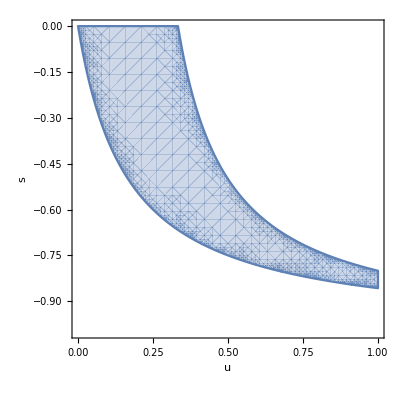

```mathematica
RegionPlot[stab1,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
jac2=jac/.sol[[2]]//Simplify
```

{{-(6 (-1+5 (1+s) u))/(6+5 s),0,0,0,0,0},{6 u,(6+s-24 u-24 s u)/(6+5 s),0,0,0,0},{0,5 u,(2 (3+s-9 u-9 s u))/(6+5 s),0,0,0},{0,0,4 u,(3 (2+s-4 u-4 s u))/(6+5 s),0,0},{0,0,0,3 u,(6+4 s-6 u-6 s u)/(6+5 s),0},{(6 (1+u) (s+6 u+6 s u))/(6+5 s),(5 (1+u) (s+6 u+6 s u))/(6+5 s),(4 (1+u) (s+6 u+6 s u))/(6+5 s),(3 (1+u) (s+6 u+6 s u))/(6+5 s),(2 (6 u (2+u)+s (1+12 u+6 u^2)))/(6+5 s),(6 (1+u+u^2)+s (6+7 u+6 u^2))/(6+5 s)}}

```mathematica
eig2=Eigenvalues[jac2]//Simplify
```

{(6+s-24 u-24 s u)/(6+5 s),(6+4 s-6 u-6 s u)/(6+5 s),(3 (2+s-4 u-4 s u))/(6+5 s),-(6 (-1+5 (1+s) u))/(6+5 s),(2 (3+s-9 u-9 s u))/(6+5 s),(6 (1+u+u^2)+s (6+7 u+6 u^2))/(6+5 s)}

```mathematica
stab2=Reduce[Flatten[{Table[-1<eig2[[i]]<1,{i,1,6}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac3=jac/.sol[[3]]//Simplify
```

{{-(3 (-1+4 (1+s) u))/(3+2 s),0,0,0,0,0},{6 u,(6+s-18 u-18 s u)/(6+4 s),0,0,0,0},{0,5 u,(3+s-6 u-6 s u)/(3+2 s),0,0,0},{0,0,4 u,(6+3 s-6 u-6 s u)/(6+4 s),0,0},{(3 (s+6 u+6 s u)^2)/(s (3+2 s)),(5 (s+6 u+6 s u)^2)/(2 s (3+2 s)),(2 (s+6 u+6 s u)^2)/(s (3+2 s)),(3 (36 u^2+18 s u (1+4 u)+s^2 (1+16 u+36 u^2)))/(2 s (3+2 s)),(3 (1+s) (s+4 s u+12 u^2+12 s u^2))/(s (3+2 s)),(s+6 u+6 s u)^2/(2 s (3+2 s))},{-(6 (6+5 s) u (s+6 u+6 s u))/(s (3+2 s)),-(5 (6+5 s) u (s+6 u+6 s u))/(s (3+2 s)),-(4 (6+5 s) u (s+6 u+6 s u))/(s (3+2 s)),-(3 (6+5 s) u (s+6 u+6 s u))/(s (3+2 s)),-(6 (1+s) u (s+12 u+10 s u))/(s (3+2 s)),(-72 u^2+s^2 (5-4 u-60 u^2)-6 s (-1+u+22 u^2))/(2 s (3+2 s))}}

```mathematica
eig3=Eigenvalues[jac3]//Simplify
```

{(6+3 s-6 u-6 s u)/(6+4 s),-(3 (-1+4 (1+s) u))/(3+2 s),(3+s-6 u-6 s u)/(3+2 s),(6+s-18 u-18 s u)/(6+4 s),(3 (1+s) (1+2 u))/(3+2 s),(6 (1+u+2 u^2)+s (5+8 u+12 u^2))/(6+4 s)}

```mathematica
stab3=Reduce[Flatten[{Table[-1<eig3[[i]]<1,{i,1,6}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac4=jac/.sol[[4]]//Simplify
```

{{(2-6 (1+s) u)/(2+s),0,0,0,0,0},{6 u,(6+s-12 u-12 s u)/(6+3 s),0,0,0,0},{0,5 u,(6+2 s-6 u-6 s u)/(6+3 s),0,0,0},{(2 (s+6 u+6 s u)^3)/(s^2 (2+s) (1+3 u)),(5 (s+6 u+6 s u)^3)/(3 s^2 (2+s) (1+3 u)),(4 (216 u^3+108 s u^2 (1+6 u)+6 s^2 u (4+39 u+108 u^2)+s^3 (1+21 u+117 u^2+216 u^3)))/(3 s^2 (2+s) (1+3 u)),(216 u^3+108 s u^2 (1+6 u)+s^3 (2+21 u+108 u^2+216 u^3)+s^2 (2+24 u+216 u^2+648 u^3))/(s^2 (2+s) (1+3 u)),(2 (s+6 u+6 s u)^3)/(3 s^2 (2+s) (1+3 u)),(s+6 u+6 s u)^3/(3 s^2 (2+s) (1+3 u))},{-(12 (3+2 s) u (s+6 u+6 s u)^2)/(s^2 (2+s) (1+3 u)),-(10 (3+2 s) u (s+6 u+6 s u)^2)/(s^2 (2+s) (1+3 u)),-(8 (3+2 s) u (s+6 u+6 s u)^2)/(s^2 (2+s) (1+3 u)),-(3 u (216 u^2+72 s u (1+8 u)+3 s^3 (1+15 u+48 u^2)+2 s^2 (2+57 u+252 u^2)))/(s^2 (2+s) (1+3 u)),-1/(3 s^2 (2+s) (1+3 u))2 (648 u^3+216 s u^2 (1+8 u)+s^3 (-2+3 u+135 u^2+432 u^3)+3 s^2 (-1+2 u+117 u^2+504 u^3)),-(2 (3+2 s) u (s+6 u+6 s u)^2)/(s^2 (2+s) (1+3 u))},{(18 (6+5 s) u^2 (s+6 u+6 s u))/(s^2 (1+3 u)),(15 (6+5 s) u^2 (s+6 u+6 s u))/(s^2 (1+3 u)),(12 (6+5 s) u^2 (s+6 u+6 s u))/(s^2 (1+3 u)),(9 (6+5 s) u^2 (s+6 u+6 s u))/(s^2 (1+3 u)),(2 u (108 u^2+18 s u (1+11 u)+s^2 (1+18 u+90 u^2)))/(s^2 (1+3 u)),(648 u^3+108 s u^2 (1+14 u)+6 s^2 (1+5 u+30 u^2+189 u^3)+s^3 (5+27 u+81 u^2+270 u^3))/(3 s^2 (2+s) (1+3 u))}}

```mathematica
eig4=Eigenvalues[jac4]//Simplify
```

{(2 (1+s) (1+3 u))/(2+s),(2-6 (1+s) u)/(2+s),(6+2 s-6 u-6 s u)/(6+3 s),(6+s-12 u-12 s u)/(6+3 s),(6+4 s+6 u+9 s u+18 u^2+18 s u^2)/(6+3 s),(6+5 s+12 u+12 s u)/(6+3 s)}

```mathematica
stab4=Reduce[Flatten[{Table[-1<eig4[[i]]<1,{i,1,6}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac5=jac/.sol[[5]]//Simplify
```

{{(3-6 (1+s) u)/(3+s),0,0,0,0,0},{6 u,(6+s-6 u-6 s u)/(6+2 s),0,0,0,0},{(3 (s+6 u+6 s u)^4)/(s^3 (3+s) (1+4 u)^2),1/(2 s^3 (3+s) (1+4 u)^2)5 (1296 u^4+864 s u^3 (1+6 u)+216 s^2 u^2 (1+6 u)^2+6 s^3 u (5+80 u+448 u^2+864 u^3)+s^4 (1+26 u+232 u^2+896 u^3+1296 u^4)),1/(s^3 (3+s) (1+4 u)^2)(2592 u^4+1728 s u^3 (1+6 u)+432 s^2 u^2 (1+6 u)^2+s^4 (3+56 u+448 u^2+1728 u^3+2592 u^4)+3 s^3 (1+24 u+304 u^2+1728 u^3+3456 u^4)),(3 (s+6 u+6 s u)^4)/(2 s^3 (3+s) (1+4 u)^2),(s+6 u+6 s u)^4/(s^3 (3+s) (1+4 u)^2),(s+6 u+6 s u)^4/(2 s^3 (3+s) (1+4 u)^2)},{-(36 (2+s) u (s+6 u+6 s u)^3)/(s^3 (3+s) (1+4 u)^2),-(30 (2+s) u (s+6 u+6 s u)^3)/(s^3 (3+s) (1+4 u)^2),-1/(s^3 (3+s) (1+4 u)^2)4 u (2592 u^3+1296 s u^2 (1+7 u)+216 s^2 u (1+15 u+54 u^2)+s^4 (5+100 u+632 u^2+1296 u^3)+3 s^3 (3+100 u+848 u^2+2160 u^3)),-1/(2 s^3 (3+s) (1+4 u)^2)3 (5184 u^4+2592 s u^3 (1+7 u)+432 s^2 u^2 (1+15 u+54 u^2)+s^4 (-1+2 u+184 u^2+1264 u^3+2592 u^4)+2 s^3 (-1+3 u+300 u^2+2576 u^3+6480 u^4)),-(12 (2+s) u (s+6 u+6 s u)^3)/(s^3 (3+s) (1+4 u)^2),-(6 (2+s) u (s+6 u+6 s u)^3)/(s^3 (3+s) (1+4 u)^2)},{(72 (3+2 s) u^2 (s+6 u+6 s u)^2)/(s^3 (1+4 u)^2),(60 (3+2 s) u^2 (s+6 u+6 s u)^2)/(s^3 (1+4 u)^2),(48 (3+2 s) u^2 (s+6 u+6 s u)^2)/(s^3 (1+4 u)^2),1/(s^3 (1+4 u)^2)3 u (1296 u^3+432 s u^2 (1+8 u)+36 s^2 u (1+20 u+84 u^2)+s^3 (1+32 u+304 u^2+864 u^3)),1/(s^3 (3+s) (1+4 u)^2)(7776 u^4+2592 s u^3 (1+9 u)+216 s^2 u^2 (1+24 u+116 u^2)+2 s^4 (1+11 u+64 u^2+336 u^3+864 u^4)+3 s^3 (1+10 u+104 u^2+1088 u^3+3744 u^4)),(12 (3+2 s) u^2 (s+6 u+6 s u)^2)/(s^3 (1+4 u)^2)},{-(48 (3+s) (6+5 s) u^3 (s+6 u+6 s u))/(s^3 (1+4 u)^2),-(40 (3+s) (6+5 s) u^3 (s+6 u+6 s u))/(s^3 (1+4 u)^2),-(32 (3+s) (6+5 s) u^3 (s+6 u+6 s u))/(s^3 (1+4 u)^2),-(24 (3+s) (6+5 s) u^3 (s+6 u+6 s u))/(s^3 (1+4 u)^2),-(2 u (864 u^3+144 s u^2 (1+13 u)+24 s^2 u^2 (7+52 u)+s^3 (-1-8 u+24 u^2+240 u^3)))/(s^3 (1+4 u)^2),-1/(2 s^3 (3+s) (1+4 u)^2)(5184 u^4+864 s u^3 (1+15 u)+432 s^2 u^3 (3+26 u)-s^4 (5+58 u+224 u^2+208 u^3-480 u^4)+6 s^3 (-1-11 u-40 u^2+48 u^3+656 u^4))}}

```mathematica
eig5=Eigenvalues[jac5]//Simplify
```

{(3 (1+s) (1+4 u))/(3+s),(3-6 (1+s) u)/(3+s),(6+s-6 u-6 s u)/(6+2 s),(3+2 s+6 u+6 s u)/(3+s),(6+5 s+18 u+18 s u)/(6+2 s),(6+3 s+6 u+10 s u+24 u^2+24 s u^2)/(6+2 s)}

```mathematica
stab5=Reduce[Flatten[{Table[-1<eig5[[i]]<1,{i,1,6}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac6=jac/.sol[[6]]//Simplify
```

{{-(6 (-1+u+s u))/(6+s),0,0,0,0,0},{1/(s^4 (6+s) (1+5 u)^3)6 (7776 u^5+6480 s u^4 (1+6 u)+2160 u^3 (s+6 s u)^2+360 u^2 (s+6 s u)^3+6 s^4 u (6+135 u+1155 u^2+4445 u^3+6480 u^4)+s^5 (1+31 u+375 u^2+2235 u^3+6605 u^4+7776 u^5)),1/(s^4 (6+s) (1+5 u)^3)(38880 u^5+32400 s u^4 (1+6 u)+10800 u^3 (s+6 s u)^2+1800 u^2 (s+6 s u)^3+6 s^4 (1+40 u+675 u^2+5525 u^3+21600 u^4+32400 u^5)+s^5 (6+165 u+1875 u^2+10925 u^3+32400 u^4+38880 u^5)),(4 (s+6 u+6 s u)^5)/(s^4 (6+s) (1+5 u)^3),(3 (s+6 u+6 s u)^5)/(s^4 (6+s) (1+5 u)^3),(2 (s+6 u+6 s u)^5)/(s^4 (6+s) (1+5 u)^3),(s+6 u+6 s u)^5/(s^4 (6+s) (1+5 u)^3)},{-(60 (3+s) u (s+6 u+6 s u)^4)/(s^4 (6+s) (1+5 u)^3),-1/(s^4 (6+s) (1+5 u)^3)5 u (38880 u^4+720 s^3 u (1+6 u)^2 (1+9 u)+12960 s u^3 (2+13 u)+2160 s^2 u^2 (3+40 u+132 u^2)+s^5 (9+225 u+2085 u^2+8515 u^3+12960 u^4)+6 s^4 (4+145 u+1725 u^2+8515 u^3+15120 u^4)),-1/(s^4 (6+s) (1+5 u)^3)2 (77760 u^5+1440 s^3 u^2 (1+6 u)^2 (1+9 u)+25920 s u^4 (2+13 u)+4320 s^2 u^3 (3+40 u+132 u^2)+s^5 (-1+2 u+360 u^2+3970 u^3+16905 u^4+25920 u^5)+3 s^4 (-1+4 u+550 u^2+7000 u^3+34435 u^4+60480 u^5)),-(30 (3+s) u (s+6 u+6 s u)^4)/(s^4 (6+s) (1+5 u)^3),-(20 (3+s) u (s+6 u+6 s u)^4)/(s^4 (6+s) (1+5 u)^3),-(10 (3+s) u (s+6 u+6 s u)^4)/(s^4 (6+s) (1+5 u)^3)},{(180 (2+s) u^2 (s+6 u+6 s u)^3)/(s^4 (1+5 u)^3),(150 (2+s) u^2 (s+6 u+6 s u)^3)/(s^4 (1+5 u)^3),1/(s^4 (1+5 u)^3)4 u (12960 u^4+6480 s u^3 (1+7 u)+60 s^3 u (1+6 u)^2 (1+15 u)+1080 s^2 u^2 (1+15 u+54 u^2)+s^4 (1+45 u+615 u^2+3365 u^3+6480 u^4)),1/(s^4 (6+s) (1+5 u)^3)3 (77760 u^5+12960 s u^4 (3+22 u)+6480 s^2 u^3 (1+16 u+61 u^2)+360 s^3 u^2 (1+30 u+261 u^2+702 u^3)+s^5 (1+19 u+165 u^2+965 u^3+3740 u^4+6480 u^5)+s^4 (2+34 u+450 u^2+5410 u^3+32900 u^4+71280 u^5)),(60 (2+s) u^2 (s+6 u+6 s u)^3)/(s^4 (1+5 u)^3),(30 (2+s) u^2 (s+6 u+6 s u)^3)/(s^4 (1+5 u)^3)},{-(120 (6+s) (3+2 s) u^3 (s+6 u+6 s u)^2)/(s^4 (1+5 u)^3),-(100 (6+s) (3+2 s) u^3 (s+6 u+6 s u)^2)/(s^4 (1+5 u)^3),-(80 (6+s) (3+2 s) u^3 (s+6 u+6 s u)^2)/(s^4 (1+5 u)^3),-1/(s^4 (1+5 u)^3)3 u (12960 u^4+2160 s u^3 (2+17 u)+360 s^2 u^2 (1+22 u+100 u^2)+60 s^3 u^2 (5+68 u+228 u^2)+s^4 (-1-15 u-35 u^2+355 u^3+1440 u^4)),-1/(s^4 (6+s) (1+5 u)^3)2 (77760 u^5+25920 s u^4 (1+9 u)+2160 s^2 u^3 (1+24 u+117 u^2)+720 s^3 u^3 (3+45 u+164 u^2)+s^5 (-2-39 u-285 u^2-885 u^3-645 u^4+1440 u^5)+3 s^4 (-1-18 u-120 u^2-170 u^3+1945 u^4+7440 u^5)),-(20 (6+s) (3+2 s) u^3 (s+6 u+6 s u)^2)/(s^4 (1+5 u)^3)},{(30 (6+s)^2 (6+5 s) u^4 (s+6 u+6 s u))/(s^4 (1+5 u)^3),(25 (6+s)^2 (6+5 s) u^4 (s+6 u+6 s u))/(s^4 (1+5 u)^3),(20 (6+s)^2 (6+5 s) u^4 (s+6 u+6 s u))/(s^4 (1+5 u)^3),(15 (6+s)^2 (6+5 s) u^4 (s+6 u+6 s u))/(s^4 (1+5 u)^3),1/(s^4 (1+5 u)^3)2 u (6480 u^4+1080 s u^3 (1+13 u)+180 s^2 u^3 (7+53 u)+30 s^3 u^3 (11+71 u)+s^4 (1+15 u+75 u^2+150 u^3+150 u^4)),1/(s^4 (6+s) (1+5 u)^3)(38880 u^5+6480 s u^4 (1+14 u)+2160 s^2 u^4 (4+33 u)+360 s^3 u^4 (9+62 u)+s^5 (5+99 u+735 u^2+2425 u^3+3025 u^4+150 u^5)+6 s^4 (1+19 u+135 u^2+425 u^3+580 u^4+505 u^5))}}

```mathematica
eig6=Eigenvalues[jac6]//Simplify
```

{(6 (1+s) (1+5 u))/(6+s),-(6 (-1+u+s u))/(6+s),(3 (2+s+4 u+4 s u))/(6+s),(2 (3+9 u+s (2+9 u)))/(6+s),(6+5 s+24 u+24 s u)/(6+s),(6 (1+u+5 u^2)+s (2+11 u+30 u^2))/(6+s)}

```mathematica
stab6=Reduce[Flatten[{Table[-1<eig6[[i]]<1,{i,1,6}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac7=jac/.sol[[7]]//Simplify
```

{{1/(s^5 (1+6 u)^4)(46656 u^6+46656 s u^5 (1+6 u)+4320 s^3 u^3 (1+6 u)^3+19440 u^4 (s+6 s u)^2+540 u^2 (s+6 s u)^4+(s+6 s u)^6+s^5 (1+6 u)^4 (1+36 u+216 u^2)),(5 (s+6 u+6 s u)^6)/(6 s^5 (1+6 u)^4),(2 (s+6 u+6 s u)^6)/(3 s^5 (1+6 u)^4),(s+6 u+6 s u)^6/(2 s^5 (1+6 u)^4),(s+6 u+6 s u)^6/(3 s^5 (1+6 u)^4),(s+6 u+6 s u)^6/(6 s^5 (1+6 u)^4)},{-1/(s^5 (1+6 u)^4)6 u (46656 u^5+s^6 (1+6 u)^5+2160 s^3 u^2 (1+6 u)^2 (1+7 u)+180 s^4 u (1+6 u)^3 (1+8 u)+7776 s u^4 (5+31 u)+s^5 (1+6 u)^4 (5+66 u)+6480 s^2 u^3 (2+25 u+78 u^2)),-1/(6 s^5 (1+6 u)^4)(1399680 u^6+64800 s^3 u^3 (1+6 u)^2 (1+7 u)+5400 s^4 u^2 (1+6 u)^3 (1+8 u)+s^6 (1+6 u)^5 (-1+30 u)+233280 s u^5 (5+31 u)+194400 s^2 u^4 (2+25 u+78 u^2)+6 s^5 (1+6 u)^4 (-1+29 u+330 u^2)),-(4 (6+s) u (s+6 u+6 s u)^5)/(s^5 (1+6 u)^4),-(3 (6+s) u (s+6 u+6 s u)^5)/(s^5 (1+6 u)^4),-(2 (6+s) u (s+6 u+6 s u)^5)/(s^5 (1+6 u)^4),-((6+s) u (s+6 u+6 s u)^5)/(s^5 (1+6 u)^4)},{(180 (3+s) u^2 (s+6 u+6 s u)^4)/(s^5 (1+6 u)^4),1/(s^5 (1+6 u)^4)5 u (116640 u^5+2160 s^3 u^2 (1+6 u)^2 (1+9 u)+38880 s u^4 (2+13 u)+90 s^4 u (1+6 u)^3 (1+14 u)+s^5 (1+6 u)^4 (1+30 u)+6480 s^2 u^3 (3+40 u+132 u^2)),1/(3 s^5 (1+6 u)^4)(1399680 u^6+s^6 (1+6 u)^5+25920 s^3 u^3 (1+6 u)^2 (1+9 u)+466560 s u^5 (2+13 u)+1080 s^4 u^2 (1+6 u)^3 (1+14 u)+3 s^5 (1+6 u)^4 (1+2 u+120 u^2)+77760 s^2 u^4 (3+40 u+132 u^2)),(90 (3+s) u^2 (s+6 u+6 s u)^4)/(s^5 (1+6 u)^4),(60 (3+s) u^2 (s+6 u+6 s u)^4)/(s^5 (1+6 u)^4),(30 (3+s) u^2 (s+6 u+6 s u)^4)/(s^5 (1+6 u)^4)},{-(2160 (2+s) u^3 (s+6 u+6 s u)^3)/(s^5 (1+6 u)^4),-(1800 (2+s) u^3 (s+6 u+6 s u)^3)/(s^5 (1+6 u)^4),-1/(s^5 (1+6 u)^4)4 u (155520 u^5+360 s^4 u^2 (1+6 u)^3-s^5 (1+6 u)^4+77760 s u^4 (1+7 u)+720 s^3 u^2 (1+6 u)^2 (1+15 u)+12960 s^2 u^3 (1+15 u+54 u^2)),-1/(2 s^5 (1+6 u)^4)(933120 u^6+2160 s^4 u^3 (1+6 u)^3-2 s^5 (1+3 u) (1+6 u)^4-s^6 (1+6 u)^5+466560 s u^5 (1+7 u)+4320 s^3 u^3 (1+6 u)^2 (1+15 u)+77760 s^2 u^4 (1+15 u+54 u^2)),-(720 (2+s) u^3 (s+6 u+6 s u)^3)/(s^5 (1+6 u)^4),-(360 (2+s) u^3 (s+6 u+6 s u)^3)/(s^5 (1+6 u)^4)},{(6480 (3+2 s) u^4 (s+6 u+6 s u)^2)/(s^5 (1+6 u)^4),(5400 (3+2 s) u^4 (s+6 u+6 s u)^2)/(s^5 (1+6 u)^4),(4320 (3+2 s) u^4 (s+6 u+6 s u)^2)/(s^5 (1+6 u)^4),1/(s^5 (1+6 u)^4)3 u (116640 u^5+2160 s^3 u^3 (1+6 u)^2+s^5 (1+6 u)^4+38880 s u^4 (1+8 u)+3240 s^2 u^3 (1+20 u+84 u^2)),1/(3 s^5 (1+6 u)^4)(699840 u^6+12960 s^3 u^4 (1+6 u)^2+3 s^5 (1+4 u) (1+6 u)^4+2 s^6 (1+6 u)^5+233280 s u^5 (1+8 u)+19440 s^2 u^4 (1+20 u+84 u^2)),(1080 (3+2 s) u^4 (s+6 u+6 s u)^2)/(s^5 (1+6 u)^4)},{-(7776 (6+5 s) u^5 (s+6 u+6 s u))/(s^5 (1+6 u)^4),-(6480 (6+5 s) u^5 (s+6 u+6 s u))/(s^5 (1+6 u)^4),-(5184 (6+5 s) u^5 (s+6 u+6 s u))/(s^5 (1+6 u)^4),-(3888 (6+5 s) u^5 (s+6 u+6 s u))/(s^5 (1+6 u)^4),(2 u (-46656 u^5-6480 s^2 u^4 (1+6 u)+s^5 (1+6 u)^4-7776 s u^4 (1+11 u)))/(s^5 (1+6 u)^4),1/(6 s^5 (1+6 u)^4)(-279936 u^6-38880 s^2 u^5 (1+6 u)+6 s^5 (1+5 u) (1+6 u)^4+5 s^6 (1+6 u)^5-46656 s u^5 (1+11 u))}}

```mathematica
eig7=Eigenvalues[jac7]//Simplify
```

{(1+s) (1+6 u),1/2 (2+s+6 u+6 s u),1/3 (3+s+6 u+6 s u),1+4 u+s (2/3+4 u),1+5 u+s (5/6+5 u),1+u+6 u^2+1/6 s (1+6 u)^2}

```mathematica
stab7=Reduce[Flatten[{Table[-1<eig7[[i]]<1,{i,1,6}],0<u<1,-1<s<0}]]
```

0<u<1&&-1<s<-(6 u)/(1+6 u)

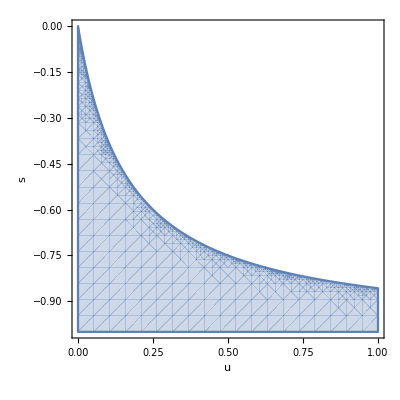

```mathematica
RegionPlot[stab7,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
k̄[6]/.sol[[7]]//Simplify
```

-(36 u)/(s+6 s u)

```mathematica
𝒱[6]/.sol[[7]]//Simplify
```

-(36 u (s+6 u+6 s u))/(s+6 s u)^2

```mathematica
𝒮[6]/.sol[[7]]//Simplify
```

-(36 u (72 u^2+18 s u (1+6 u)+(s+6 s u)^2))/(s+6 s u)^3

### n=7

```mathematica
nextf=f[7]+delta[7,s,u];
```

```mathematica
sol=Solve[Table[nextf[[k+1]]==Subscript[f, k],{k,0,6}],Table[Subscript[f, k],{k,0,6}]]//Simplify
```

{{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→0},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→(s+7 u+7 s u)/(s+s u)},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→(s+7 u+7 s u)^2/(s+2 s u)^2,f_6→-(2 (7+5 s) u (s+7 u+7 s u))/(s+2 s u)^2},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→(s+7 u+7 s u)^3/(s+3 s u)^3,f_5→-(3 (7+4 s) u (s+7 u+7 s u)^2)/(s+3 s u)^3,f_6→(3 (7+4 s)^2 u^2 (s+7 u+7 s u))/(s+3 s u)^3},{f_0→0,f_1→0,f_2→0,f_3→(s+7 u+7 s u)^4/(s+4 s u)^4,f_4→-(4 (7+3 s) u (s+7 u+7 s u)^3)/(s+4 s u)^4,f_5→(6 (7+3 s)^2 u^2 (s+7 u+7 s u)^2)/(s+4 s u)^4,f_6→-(4 (7+3 s)^3 u^3 (s+7 u+7 s u))/(s+4 s u)^4},{f_0→0,f_1→0,f_2→(s+7 u+7 s u)^5/(s+5 s u)^5,f_3→-(5 (7+2 s) u (s+7 u+7 s u)^4)/(s+5 s u)^5,f_4→(10 (7+2 s)^2 u^2 (s+7 u+7 s u)^3)/(s+5 s u)^5,f_5→-(10 (7+2 s)^3 u^3 (s+7 u+7 s u)^2)/(s+5 s u)^5,f_6→(5 (7+2 s)^4 u^4 (s+7 u+7 s u))/(s+5 s u)^5},{f_0→0,f_1→(s+7 u+7 s u)^6/(s+6 s u)^6,f_2→-(6 (7+s) u (s+7 u+7 s u)^5)/(s+6 s u)^6,f_3→(15 (7+s)^2 u^2 (s+7 u+7 s u)^4)/(s+6 s u)^6,f_4→-(20 (7+s)^3 u^3 (s+7 u+7 s u)^3)/(s+6 s u)^6,f_5→(15 (7+s)^4 u^4 (s+7 u+7 s u)^2)/(s+6 s u)^6,f_6→-(6 (7+s)^5 u^5 (s+7 u+7 s u))/(s+6 s u)^6},{f_0→(s+7 u+7 s u)^7/(s+7 s u)^7,f_1→-(49 u (s+7 u+7 s u)^6)/(s+7 s u)^7,f_2→(1029 u^2 (s+7 u+7 s u)^5)/(s+7 s u)^7,f_3→-(12005 u^3 (s+7 u+7 s u)^4)/(s+7 s u)^7,f_4→(84035 u^4 (s+7 u+7 s u)^3)/(s+7 s u)^7,f_5→-(352947 u^5 (s+7 u+7 s u)^2)/(s+7 s u)^7,f_6→(823543 u^6 (s+7 u+7 s u))/(s+7 s u)^7}}

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→0},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0,f_6→0.936064},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0,f_5→0.874468,f_6→0.121324},{f_0→0,f_1→0,f_2→0,f_3→0,f_4→0.815297,f_5→0.172283,f_6→0.0121352},{f_0→0,f_1→0,f_2→0,f_3→0.758619,f_4→0.21698,f_5→0.0232726,f_6→0.0011094},{f_0→0,f_1→0,f_2→0.704478,f_3→0.255627,f_4→0.0371028,f_5→0.00269262,f_6→0.0000977046},{f_0→0,f_1→0.652904,f_2→0.288476,f_3→0.053108,f_4→0.00521445,f_5→0.000287991,f_6→8.48298×10^-6},{f_0→0.603908,f_1→0.315811,f_2→0.0707794,f_3→0.00881281,f_4→0.000658374,f_5→0.0000295109,f_6→7.34885×10^-7}}

```mathematica
sol[[8]]==eq[7,s,u]//Simplify
```

True

```mathematica
valid7=Table[{Reduce[{0≤Values[sol[[i]][[1]]]≤1,0<u<1,-1<s<0}]},{i,1,8}]
```

{{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s<0},{0<u<1&&-1<s≤-(7 u)/(1+7 u)}}

```mathematica
jac=Table[Table[D[nextf[[i]],Subscript[f, j]],{j,0,6}],{i,1,7}]//Simplify
```

{{(7 (-7 s u f_0 (-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)+7 s f_0 (1-7 u-7 s u+7 s u f_0+6 s u f_1+5 s u f_2+4 s u f_3+3 s u f_4+2 s u f_5+s u f_6)-(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6) (1-7 u-7 s u+7 s u f_0+6 s u f_1+5 s u f_2+4 s u f_3+3 s u f_4+2 s u f_5+s u f_6)))/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(42 s f_0)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(35 s f_0)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(28 s f_0)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(21 s f_0)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(14 s f_0)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(7 s f_0)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2},{7 (u+(s (7+s) f_1)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2),-6 u+(6 s (7+s) f_1)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2-(7+s)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6),(5 s (7+s) f_1)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(4 s (7+s) f_1)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(3 s (7+s) f_1)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(2 s (7+s) f_1)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(s (7+s) f_1)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2},{(7 s (7+2 s) f_2)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,6 (u+(s (7+2 s) f_2)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2),-5 u+(5 s (7+2 s) f_2)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2+(-7-2 s)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6),(4 s (7+2 s) f_2)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(3 s (7+2 s) f_2)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(2 s (7+2 s) f_2)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(s (7+2 s) f_2)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2},{(7 s (7+3 s) f_3)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(6 s (7+3 s) f_3)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,5 (u+(s (7+3 s) f_3)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2),-4 u+(4 s (7+3 s) f_3)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2+(-7-3 s)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6),(3 s (7+3 s) f_3)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(2 s (7+3 s) f_3)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(s (7+3 s) f_3)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2},{(7 s (7+4 s) f_4)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(6 s (7+4 s) f_4)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(5 s (7+4 s) f_4)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,4 (u+(s (7+4 s) f_4)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2),-3 u+(3 s (7+4 s) f_4)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2+(-7-4 s)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6),(2 s (7+4 s) f_4)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(s (7+4 s) f_4)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2},{(7 s (7+5 s) f_5)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(6 s (7+5 s) f_5)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(5 s (7+5 s) f_5)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(4 s (7+5 s) f_5)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,3 (u+(s (7+5 s) f_5)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2),-2 u+(2 s (7+5 s) f_5)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2+(-7-5 s)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6),(s (7+5 s) f_5)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2},{(7 s (7+6 s) f_6)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(6 s (7+6 s) f_6)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(5 s (7+6 s) f_6)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(4 s (7+6 s) f_6)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,(3 s (7+6 s) f_6)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2,2 (u+(s (7+6 s) f_6)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2),-u+(s (7+6 s) f_6)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)^2+(-7-6 s)/(-7-7 s+7 s f_0+6 s f_1+5 s f_2+4 s f_3+3 s f_4+2 s f_5+s f_6)}}

```mathematica
jac1=jac/.sol[[1]]//Simplify
```

{{(1-7 (1+s) u)/(1+s),0,0,0,0,0,0},{7 u,(7+s)/(7+7 s)-6 u,0,0,0,0,0},{0,6 u,(7+2 s)/(7+7 s)-5 u,0,0,0,0},{0,0,5 u,(7+3 s)/(7+7 s)-4 u,0,0,0},{0,0,0,4 u,(7+4 s)/(7+7 s)-3 u,0,0},{0,0,0,0,3 u,(7+5 s)/(7+7 s)-2 u,0},{0,0,0,0,0,2 u,(7+6 s)/(7+7 s)-u}}

```mathematica
eig1=Eigenvalues[jac1]//Simplify
```

{(7+s-42 u-42 s u)/(7+7 s),(7+2 s-35 u-35 s u)/(7+7 s),(7+3 s-28 u-28 s u)/(7+7 s),(7+4 s-21 u-21 s u)/(7+7 s),(7+5 s-14 u-14 s u)/(7+7 s),(7+6 s-7 u-7 s u)/(7+7 s),(1-7 (1+s) u)/(1+s)}

```mathematica
stab1=Reduce[Flatten[{Table[-1<eig1[[i]]<1,{i,1,7}],0<u<1,-1<s<0}]]
```

(0<u≤2/7&&-(7 u)/(1+7 u)<s<0)||(2/7<u<1&&-(7 u)/(1+7 u)<s<(2-7 u)/(-1+7 u))

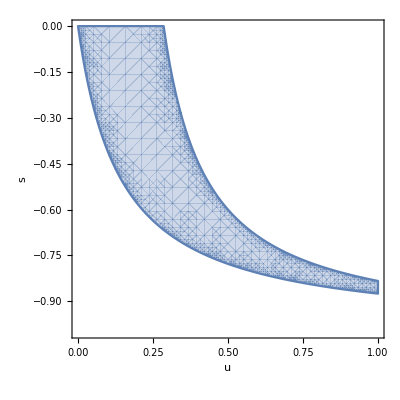

```mathematica
RegionPlot[stab1,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
jac2=jac/.sol[[2]]//Simplify
```

{{-(7 (-1+6 (1+s) u))/(7+6 s),0,0,0,0,0,0},{7 u,(7+s-35 u-35 s u)/(7+6 s),0,0,0,0,0},{0,6 u,(7+2 s-28 u-28 s u)/(7+6 s),0,0,0,0},{0,0,5 u,(7+3 s-21 u-21 s u)/(7+6 s),0,0,0},{0,0,0,4 u,(7+4 s-14 u-14 s u)/(7+6 s),0,0},{0,0,0,0,3 u,(7+5 s-7 u-7 s u)/(7+6 s),0},{(7 (1+u) (s+7 u+7 s u))/(7+6 s),(6 (1+u) (s+7 u+7 s u))/(7+6 s),(5 (1+u) (s+7 u+7 s u))/(7+6 s),(4 (1+u) (s+7 u+7 s u))/(7+6 s),(3 (1+u) (s+7 u+7 s u))/(7+6 s),(2 (7 u (2+u)+s (1+14 u+7 u^2)))/(7+6 s),(7 (1+u+u^2)+s (7+8 u+7 u^2))/(7+6 s)}}

```mathematica
eig2=Eigenvalues[jac2]//Simplify
```

{(7+s-35 u-35 s u)/(7+6 s),(7+2 s-28 u-28 s u)/(7+6 s),(7+3 s-21 u-21 s u)/(7+6 s),(7+4 s-14 u-14 s u)/(7+6 s),(7+5 s-7 u-7 s u)/(7+6 s),-(7 (-1+6 (1+s) u))/(7+6 s),(7 (1+u+u^2)+s (7+8 u+7 u^2))/(7+6 s)}

```mathematica
stab2=Reduce[Flatten[{Table[-1<eig2[[i]]<1,{i,1,7}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac3=jac/.sol[[3]]//Simplify
```

{{-(7 (-1+5 (1+s) u))/(7+5 s),0,0,0,0,0,0},{7 u,(7+s-28 u-28 s u)/(7+5 s),0,0,0,0,0},{0,6 u,(7+2 s-21 u-21 s u)/(7+5 s),0,0,0,0},{0,0,5 u,(7+3 s-14 u-14 s u)/(7+5 s),0,0,0},{0,0,0,4 u,(7+4 s-7 u-7 s u)/(7+5 s),0,0},{(7 (s+7 u+7 s u)^2)/(s (7+5 s)),(6 (s+7 u+7 s u)^2)/(s (7+5 s)),(5 (s+7 u+7 s u)^2)/(s (7+5 s)),(4 (s+7 u+7 s u)^2)/(s (7+5 s)),(3 (49 u^2+7 s u (3+14 u)+s^2 (1+19 u+49 u^2)))/(s (7+5 s)),(7 (1+s) (s+4 s u+14 u^2+14 s u^2))/(s (7+5 s)),(s+7 u+7 s u)^2/(s (7+5 s))},{-(14 (7+6 s) u (s+7 u+7 s u))/(s (7+5 s)),-(12 (7+6 s) u (s+7 u+7 s u))/(s (7+5 s)),-(10 (7+6 s) u (s+7 u+7 s u))/(s (7+5 s)),-(8 (7+6 s) u (s+7 u+7 s u))/(s (7+5 s)),-(6 (7+6 s) u (s+7 u+7 s u))/(s (7+5 s)),-(14 (1+s) u (s+14 u+12 s u))/(s (7+5 s)),(-98 u^2+s^2 (6-5 u-84 u^2)-7 s (-1+u+26 u^2))/(s (7+5 s))}}

```mathematica
eig3=Eigenvalues[jac3]//Simplify
```

{-(7 (-1+5 (1+s) u))/(7+5 s),(7+4 s-7 u-7 s u)/(7+5 s),(7+3 s-14 u-14 s u)/(7+5 s),(7+2 s-21 u-21 s u)/(7+5 s),(7+s-28 u-28 s u)/(7+5 s),(7 (1+s) (1+2 u))/(7+5 s),(7 (1+u+2 u^2)+s (6+9 u+14 u^2))/(7+5 s)}

```mathematica
stab3=Reduce[Flatten[{Table[-1<eig3[[i]]<1,{i,1,7}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac4=jac/.sol[[4]]//Simplify
```

{{-(7 (-1+4 (1+s) u))/(7+4 s),0,0,0,0,0,0},{7 u,(7+s-21 u-21 s u)/(7+4 s),0,0,0,0,0},{0,6 u,(7+2 s-14 u-14 s u)/(7+4 s),0,0,0,0},{0,0,5 u,(7+3 s-7 u-7 s u)/(7+4 s),0,0,0},{(7 (s+7 u+7 s u)^3)/(s^2 (7+4 s) (1+3 u)),(6 (s+7 u+7 s u)^3)/(s^2 (7+4 s) (1+3 u)),(5 (s+7 u+7 s u)^3)/(s^2 (7+4 s) (1+3 u)),(4 (343 u^3+147 s u^2 (1+7 u)+7 s^2 u (4+45 u+147 u^2)+s^3 (1+25 u+159 u^2+343 u^3)))/(s^2 (7+4 s) (1+3 u)),1/(s^2 (7+4 s) (1+3 u))(1029 u^3+441 s u^2 (1+7 u)+7 s^2 (1+12 u+126 u^2+441 u^3)+s^3 (7+75 u+441 u^2+1029 u^3)),(2 (s+7 u+7 s u)^3)/(s^2 (7+4 s) (1+3 u)),(s+7 u+7 s u)^3/(s^2 (7+4 s) (1+3 u))},{-(21 (7+5 s) u (s+7 u+7 s u)^2)/(s^2 (7+4 s) (1+3 u)),-(18 (7+5 s) u (s+7 u+7 s u)^2)/(s^2 (7+4 s) (1+3 u)),-(15 (7+5 s) u (s+7 u+7 s u)^2)/(s^2 (7+4 s) (1+3 u)),-(12 (7+5 s) u (s+7 u+7 s u)^2)/(s^2 (7+4 s) (1+3 u)),-(3 u (1029 u^2+147 s u (2+19 u)+7 s^2 (2+69 u+357 u^2)+s^3 (11+198 u+735 u^2)))/(s^2 (7+4 s) (1+3 u)),-1/(s^2 (7+4 s) (1+3 u))(2058 u^3+294 s u^2 (2+19 u)+7 s^2 (-1+2 u+141 u^2+714 u^3)+s^3 (-5+8 u+399 u^2+1470 u^3)),-(3 (7+5 s) u (s+7 u+7 s u)^2)/(s^2 (7+4 s) (1+3 u))},{(21 (7+6 s) u^2 (s+7 u+7 s u))/(s^2 (1+3 u)),(18 (7+6 s) u^2 (s+7 u+7 s u))/(s^2 (1+3 u)),(15 (7+6 s) u^2 (s+7 u+7 s u))/(s^2 (1+3 u)),(12 (7+6 s) u^2 (s+7 u+7 s u))/(s^2 (1+3 u)),(9 (7+6 s) u^2 (s+7 u+7 s u))/(s^2 (1+3 u)),(2 u (147 u^2+21 s u (1+13 u)+s^2 (1+21 u+126 u^2)))/(s^2 (1+3 u)),1/(s^2 (7+4 s) (1+3 u))(1029 u^3+147 s u^2 (1+17 u)+2 s^3 (3+16 u+57 u^2+252 u^3)+7 s^2 (1+5 u+36 u^2+282 u^3))}}

```mathematica
eig4=Eigenvalues[jac4]//Simplify
```

{(7 (1+s) (1+3 u))/(7+4 s),-(7 (-1+4 (1+s) u))/(7+4 s),(7+3 s-7 u-7 s u)/(7+4 s),(7+2 s-14 u-14 s u)/(7+4 s),(7+s-21 u-21 s u)/(7+4 s),(7 (1+u+3 u^2)+s (5+10 u+21 u^2))/(7+4 s),(7+6 s+14 u+14 s u)/(7+4 s)}

```mathematica
stab4=Reduce[Flatten[{Table[-1<eig4[[i]]<1,{i,1,7}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac5=jac/.sol[[5]]//Simplify
```

{{-(7 (-1+3 (1+s) u))/(7+3 s),0,0,0,0,0,0},{7 u,(7+s-14 u-14 s u)/(7+3 s),0,0,0,0,0},{0,6 u,(7+2 s-7 u-7 s u)/(7+3 s),0,0,0,0},{(7 (s+7 u+7 s u)^4)/(s^3 (7+3 s) (1+4 u)^2),(6 (s+7 u+7 s u)^4)/(s^3 (7+3 s) (1+4 u)^2),1/(s^3 (7+3 s) (1+4 u)^2)5 (2401 u^4+1372 s u^3 (1+7 u)+294 s^2 u^2 (1+7 u)^2+7 s^3 u (5+92 u+604 u^2+1372 u^3)+s^4 (1+31 u+318 u^2+1420 u^3+2401 u^4)),1/(s^3 (7+3 s) (1+4 u)^2)(9604 u^4+5488 s u^3 (1+7 u)+1176 s^2 u^2 (1+7 u)^2+7 s^3 (1+24 u+352 u^2+2352 u^3+5488 u^4)+s^4 (7+136 u+1224 u^2+5488 u^3+9604 u^4)),(3 (s+7 u+7 s u)^4)/(s^3 (7+3 s) (1+4 u)^2),(2 (s+7 u+7 s u)^4)/(s^3 (7+3 s) (1+4 u)^2),(s+7 u+7 s u)^4/(s^3 (7+3 s) (1+4 u)^2)},{-(28 (7+4 s) u (s+7 u+7 s u)^3)/(s^3 (7+3 s) (1+4 u)^2),-(24 (7+4 s) u (s+7 u+7 s u)^3)/(s^3 (7+3 s) (1+4 u)^2),-(20 (7+4 s) u (s+7 u+7 s u)^3)/(s^3 (7+3 s) (1+4 u)^2),-1/(s^3 (7+3 s) (1+4 u)^2)4 u (9604 u^3+1372 s u^2 (3+25 u)+588 s^2 u (1+18 u+77 u^2)+7 s^3 (3+124 u+1244 u^2+3724 u^3)+s^4 (13+312 u+2304 u^2+5488 u^3)),-1/(s^3 (7+3 s) (1+4 u)^2)(28812 u^4+4116 s u^3 (3+25 u)+1764 s^2 u^2 (1+18 u+77 u^2)+7 s^3 (-1+3 u+372 u^2+3764 u^3+11172 u^4)+s^4 (-4+9 u+888 u^2+6944 u^3+16464 u^4)),-(8 (7+4 s) u (s+7 u+7 s u)^3)/(s^3 (7+3 s) (1+4 u)^2),-(4 (7+4 s) u (s+7 u+7 s u)^3)/(s^3 (7+3 s) (1+4 u)^2)},{(42 (7+5 s) u^2 (s+7 u+7 s u)^2)/(s^3 (1+4 u)^2),(36 (7+5 s) u^2 (s+7 u+7 s u)^2)/(s^3 (1+4 u)^2),(30 (7+5 s) u^2 (s+7 u+7 s u)^2)/(s^3 (1+4 u)^2),(24 (7+5 s) u^2 (s+7 u+7 s u)^2)/(s^3 (1+4 u)^2),1/(s^3 (1+4 u)^2)3 u (2058 u^3+294 s u^2 (2+19 u)+42 s^2 u (1+24 u+119 u^2)+s^3 (1+38 u+436 u^2+1470 u^3)),1/(s^3 (7+3 s) (1+4 u)^2)(28812 u^4+8232 s u^3 (1+11 u)+588 s^2 u^2 (1+30 u+176 u^2)+7 s^3 (1+10 u+128 u^2+1736 u^3+7224 u^4)+s^4 (5+54 u+372 u^2+2744 u^3+8820 u^4)),(6 (7+5 s) u^2 (s+7 u+7 s u)^2)/(s^3 (1+4 u)^2)},{-(28 (7+3 s) (7+6 s) u^3 (s+7 u+7 s u))/(s^3 (1+4 u)^2),-(24 (7+3 s) (7+6 s) u^3 (s+7 u+7 s u))/(s^3 (1+4 u)^2),-(20 (7+3 s) (7+6 s) u^3 (s+7 u+7 s u))/(s^3 (1+4 u)^2),-(16 (7+3 s) (7+6 s) u^3 (s+7 u+7 s u))/(s^3 (1+4 u)^2),-(12 (7+3 s) (7+6 s) u^3 (s+7 u+7 s u))/(s^3 (1+4 u)^2),-(2 u (1372 u^3+252 s^2 u^2 (1+9 u)+196 s u^2 (1+16 u)+s^3 (-1-8 u+56 u^2+504 u^3)))/(s^3 (1+4 u)^2),1/(s^3 (7+3 s) (1+4 u)^2)(-9604 u^4-1372 s u^3 (1+19 u)-588 s^2 u^3 (4+43 u)+s^3 (7+77 u+280 u^2-924 u^3-10332 u^4)+3 s^4 (2+23 u+88 u^2+40 u^3-504 u^4))}}

```mathematica
eig5=Eigenvalues[jac5]//Simplify
```

{(7 (1+s) (1+4 u))/(7+3 s),-(7 (-1+3 (1+s) u))/(7+3 s),(7+2 s-7 u-7 s u)/(7+3 s),(7+s-14 u-14 s u)/(7+3 s),(7+5 s+14 u+14 s u)/(7+3 s),(7+6 s+21 u+21 s u)/(7+3 s),(7 (1+u+4 u^2)+s (4+11 u+28 u^2))/(7+3 s)}

```mathematica
stab5=Reduce[Flatten[{Table[-1<eig5[[i]]<1,{i,1,7}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac6=jac/.sol[[6]]//Simplify
```

{{-(7 (-1+2 (1+s) u))/(7+2 s),0,0,0,0,0,0},{7 u,(7+s-7 u-7 s u)/(7+2 s),0,0,0,0,0},{(7 (s+7 u+7 s u)^5)/(s^4 (7+2 s) (1+5 u)^3),1/(s^4 (7+2 s) (1+5 u)^3)6 (16807 u^5+12005 s u^4 (1+7 u)+3430 u^3 (s+7 s u)^2+490 u^2 (s+7 s u)^3+7 s^4 u (6+155 u+1545 u^2+6985 u^3+12005 u^4)+s^5 (1+37 u+520 u^2+3580 u^3+12255 u^4+16807 u^5)),1/(s^4 (7+2 s) (1+5 u)^3)(84035 u^5+60025 s u^4 (1+7 u)+17150 u^3 (s+7 s u)^2+2450 u^2 (s+7 s u)^3+7 s^4 (1+40 u+775 u^2+7475 u^3+34300 u^4+60025 u^5)+s^5 (7+205 u+2600 u^2+17400 u^3+60025 u^4+84035 u^5)),(4 (s+7 u+7 s u)^5)/(s^4 (7+2 s) (1+5 u)^3),(3 (s+7 u+7 s u)^5)/(s^4 (7+2 s) (1+5 u)^3),(2 (s+7 u+7 s u)^5)/(s^4 (7+2 s) (1+5 u)^3),(s+7 u+7 s u)^5/(s^4 (7+2 s) (1+5 u)^3)},{-(35 (7+3 s) u (s+7 u+7 s u)^4)/(s^4 (7+2 s) (1+5 u)^3),-(30 (7+3 s) u (s+7 u+7 s u)^4)/(s^4 (7+2 s) (1+5 u)^3),-1/(s^4 (7+2 s) (1+5 u)^3)5 u (84035 u^4+490 s^3 u (1+7 u)^2 (2+23 u)+12005 s u^3 (4+31 u)+10290 s^2 u^2 (1+16 u+63 u^2)+7 s^4 (4+185 u+2655 u^2+15555 u^3+32585 u^4)+s^5 (13+390 u+4260 u^2+20330 u^3+36015 u^4)),-1/(s^4 (7+2 s) (1+5 u)^3)(336140 u^5+1960 s^3 u^2 (1+7 u)^2 (2+23 u)+48020 s u^4 (4+31 u)+41160 s^2 u^3 (1+16 u+63 u^2)+7 s^4 (-1+4 u+710 u^2+10720 u^3+62595 u^4+130340 u^5)+s^5 (-3+8 u+1350 u^2+16740 u^3+81445 u^4+144060 u^5)),-(15 (7+3 s) u (s+7 u+7 s u)^4)/(s^4 (7+2 s) (1+5 u)^3),-(10 (7+3 s) u (s+7 u+7 s u)^4)/(s^4 (7+2 s) (1+5 u)^3),-(5 (7+3 s) u (s+7 u+7 s u)^4)/(s^4 (7+2 s) (1+5 u)^3)},{(70 (7+4 s) u^2 (s+7 u+7 s u)^3)/(s^4 (1+5 u)^3),(60 (7+4 s) u^2 (s+7 u+7 s u)^3)/(s^4 (1+5 u)^3),(50 (7+4 s) u^2 (s+7 u+7 s u)^3)/(s^4 (1+5 u)^3),1/(s^4 (1+5 u)^3)4 u (24010 u^4+70 s^3 u (1+7 u)^2 (1+19 u)+3430 s u^3 (3+25 u)+1470 s^2 u^2 (1+18 u+77 u^2)+s^4 (1+55 u+915 u^2+6005 u^3+13720 u^4)),1/(s^4 (7+2 s) (1+5 u)^3)(504210 u^5+216090 s u^4 (1+9 u)+10290 s^2 u^3 (3+60 u+281 u^2)+1470 s^3 u^2 (1+39 u+423 u^2+1393 u^3)+s^5 (4+74 u+750 u^2+6590 u^3+37030 u^4+82320 u^5)+7 s^4 (1+17 u+285 u^2+4775 u^3+36790 u^4+97020 u^5)),(20 (7+4 s) u^2 (s+7 u+7 s u)^3)/(s^4 (1+5 u)^3),(10 (7+4 s) u^2 (s+7 u+7 s u)^3)/(s^4 (1+5 u)^3)},{-(70 (7+2 s) (7+5 s) u^3 (s+7 u+7 s u)^2)/(s^4 (1+5 u)^3),-(60 (7+2 s) (7+5 s) u^3 (s+7 u+7 s u)^2)/(s^4 (1+5 u)^3),-(50 (7+2 s) (7+5 s) u^3 (s+7 u+7 s u)^2)/(s^4 (1+5 u)^3),-(40 (7+2 s) (7+5 s) u^3 (s+7 u+7 s u)^2)/(s^4 (1+5 u)^3),-1/(s^4 (1+5 u)^3)3 u (24010 u^4+3430 s u^3 (2+21 u)+490 s^2 u^2 (1+28 u+157 u^2)+70 s^3 u^2 (7+118 u+483 u^2)+s^4 (-1-15 u+25 u^2+1275 u^3+4900 u^4)),-1/(s^4 (7+2 s) (1+5 u)^3)(336140 u^5+48020 s u^4 (2+23 u)+6860 s^2 u^3 (1+32 u+199 u^2)+980 s^3 u^3 (9+174 u+797 u^2)+s^5 (-5-96 u-690 u^2-1800 u^3+2975 u^4+19600 u^5)+7 s^4 (-1-18 u-120 u^2+130 u^3+7145 u^4+29120 u^5)),-(10 (7+2 s) (7+5 s) u^3 (s+7 u+7 s u)^2)/(s^4 (1+5 u)^3)},{(35 (7+2 s)^2 (7+6 s) u^4 (s+7 u+7 s u))/(s^4 (1+5 u)^3),(30 (7+2 s)^2 (7+6 s) u^4 (s+7 u+7 s u))/(s^4 (1+5 u)^3),(25 (7+2 s)^2 (7+6 s) u^4 (s+7 u+7 s u))/(s^4 (1+5 u)^3),(20 (7+2 s)^2 (7+6 s) u^4 (s+7 u+7 s u))/(s^4 (1+5 u)^3),(15 (7+2 s)^2 (7+6 s) u^4 (s+7 u+7 s u))/(s^4 (1+5 u)^3),1/(s^4 (1+5 u)^3)2 u (12005 u^4+1715 s u^3 (1+17 u)+490 s^2 u^3 (5+49 u)+140 s^3 u^3 (7+55 u)+s^4 (1+15 u+75 u^2+245 u^3+840 u^4)),1/(s^4 (7+2 s) (1+5 u)^3)(84035 u^5+20580 s^2 u^4 (1+11 u)+12005 s u^4 (1+19 u)+3920 s^3 u^4 (3+26 u)+2 s^5 (3+59 u+435 u^2+1425 u^3+1870 u^4+840 u^5)+7 s^4 (1+19 u+135 u^2+425 u^3+900 u^4+3040 u^5))}}

```mathematica
eig6=Eigenvalues[jac6]//Simplify
```

{(7 (1+s) (1+5 u))/(7+2 s),-(7 (-1+2 (1+s) u))/(7+2 s),(7+s-7 u-7 s u)/(7+2 s),(7+4 s+14 u+14 s u)/(7+2 s),(7+5 s+21 u+21 s u)/(7+2 s),(7+6 s+28 u+28 s u)/(7+2 s),(7 (1+u+5 u^2)+s (3+12 u+35 u^2))/(7+2 s)}

```mathematica
stab6=Reduce[Flatten[{Table[-1<eig6[[i]]<1,{i,1,7}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac7=jac/.sol[[7]]//Simplify
```

{{-(7 (-1+u+s u))/(7+s),0,0,0,0,0,0},{1/(s^5 (7+s) (1+6 u)^4)7 (117649 u^6+100842 s u^5 (1+7 u)+6860 s^3 u^3 (1+7 u)^3+36015 u^4 (s+7 s u)^2+735 u^2 (s+7 s u)^4+7 s^5 u (7+234 u+3156 u^2+21444 u^3+73326 u^4+100842 u^5)+s^6 (1+43 u+759 u^2+7076 u^3+36879 u^4+102138 u^5+117649 u^6)),1/(s^5 (7+s) (1+6 u)^4)(705894 u^6+605052 s u^5 (1+7 u)+41160 s^3 u^3 (1+7 u)^3+216090 u^4 (s+7 s u)^2+4410 u^2 (s+7 s u)^4+7 s^5 (1+60 u+1476 u^2+18504 u^3+124776 u^4+432180 u^5+605052 u^6)+s^6 (7+276 u+4626 u^2+42024 u^3+217386 u^4+605052 u^5+705894 u^6)),(5 (s+7 u+7 s u)^6)/(s^5 (7+s) (1+6 u)^4),(4 (s+7 u+7 s u)^6)/(s^5 (7+s) (1+6 u)^4),(3 (s+7 u+7 s u)^6)/(s^5 (7+s) (1+6 u)^4),(2 (s+7 u+7 s u)^6)/(s^5 (7+s) (1+6 u)^4),(s+7 u+7 s u)^6/(s^5 (7+s) (1+6 u)^4)},{-(42 (7+2 s) u (s+7 u+7 s u)^5)/(s^5 (7+s) (1+6 u)^4),-1/(s^5 (7+s) (1+6 u)^4)6 u (705894 u^5+20580 s^3 u^2 (1+7 u)^2 (1+9 u)+1470 s^4 u (1+7 u)^3 (1+11 u)+100842 s u^4 (5+37 u)+144060 s^2 u^3 (1+15 u+56 u^2)+s^6 (11+396 u+5664 u^2+40296 u^3+142764 u^4+201684 u^5)+7 s^5 (5+246 u+4404 u^2+37356 u^3+153054 u^4+244902 u^5)),-1/(s^5 (7+s) (1+6 u)^4)(3529470 u^6+102900 s^3 u^3 (1+7 u)^2 (1+9 u)+7350 s^4 u^2 (1+7 u)^3 (1+11 u)+504210 s u^5 (5+37 u)+720300 s^2 u^4 (1+15 u+56 u^2)+s^6 (-2+5 u+1500 u^2+26160 u^3+197160 u^4+711228 u^5+1008420 u^6)+7 s^5 (-1+5 u+1110 u^2+22020 u^3+188940 u^4+770454 u^5+1224510 u^6)),-(24 (7+2 s) u (s+7 u+7 s u)^5)/(s^5 (7+s) (1+6 u)^4),-(18 (7+2 s) u (s+7 u+7 s u)^5)/(s^5 (7+s) (1+6 u)^4),-(12 (7+2 s) u (s+7 u+7 s u)^5)/(s^5 (7+s) (1+6 u)^4),-(6 (7+2 s) u (s+7 u+7 s u)^5)/(s^5 (7+s) (1+6 u)^4)},{(105 (7+3 s) u^2 (s+7 u+7 s u)^4)/(s^5 (1+6 u)^4),(90 (7+3 s) u^2 (s+7 u+7 s u)^4)/(s^5 (1+6 u)^4),1/(s^5 (1+6 u)^4)5 u (252105 u^5+105 s^4 u (1+7 u)^3 (1+19 u)+1470 s^3 u^2 (1+7 u)^2 (2+23 u)+36015 s u^4 (4+31 u)+30870 s^2 u^3 (1+16 u+63 u^2)+s^5 (1+69 u+1476 u^2+14094 u^3+63036 u^4+108045 u^5)),1/(s^5 (7+s) (1+6 u)^4)(7058940 u^6+4033680 s u^5 (1+8 u)+2940 s^4 u^2 (1+7 u)^2 (1+30 u+179 u^2)+144060 s^2 u^4 (6+100 u+409 u^2)+82320 s^3 u^3 (1+27 u+234 u^2+658 u^3)+s^6 (3+86 u+1164 u^2+10656 u^3+68904 u^4+265104 u^5+432180 u^6)+7 s^5 (1+26 u+504 u^2+8736 u^3+88704 u^4+437712 u^5+823200 u^6)),(45 (7+3 s) u^2 (s+7 u+7 s u)^4)/(s^5 (1+6 u)^4),(30 (7+3 s) u^2 (s+7 u+7 s u)^4)/(s^5 (1+6 u)^4),(15 (7+3 s) u^2 (s+7 u+7 s u)^4)/(s^5 (1+6 u)^4)},{-(140 (7+s) (7+4 s) u^3 (s+7 u+7 s u)^3)/(s^5 (1+6 u)^4),-(120 (7+s) (7+4 s) u^3 (s+7 u+7 s u)^3)/(s^5 (1+6 u)^4),-(100 (7+s) (7+4 s) u^3 (s+7 u+7 s u)^3)/(s^5 (1+6 u)^4),-1/(s^5 (1+6 u)^4)4 u (336140 u^5+48020 s u^4 (3+26 u)+140 s^4 u^2 (1+7 u)^2 (5+47 u)+6860 s^2 u^3 (3+57 u+256 u^2)+980 s^3 u^2 (1+36 u+369 u^2+1162 u^3)+s^5 (-1-24 u-136 u^2+816 u^3+10464 u^4+27440 u^5)),-1/(s^5 (7+s) (1+6 u)^4)(7058940 u^6+3025260 s u^5 (1+9 u)+432180 s^2 u^4 (1+20 u+94 u^2)+8820 s^4 u^3 (2+51 u+424 u^2+1155 u^3)+20580 s^3 u^3 (1+39 u+426 u^2+1418 u^3)-s^6 (4+117 u+1368 u^2+7752 u^3+18288 u^4-8064 u^5-82320 u^6)+7 s^5 (-1-27 u-288 u^2-972 u^3+8172 u^4+85572 u^5+220500 u^6)),-(40 (7+s) (7+4 s) u^3 (s+7 u+7 s u)^3)/(s^5 (1+6 u)^4),-(20 (7+s) (7+4 s) u^3 (s+7 u+7 s u)^3)/(s^5 (1+6 u)^4)},{(105 (7+s)^2 (7+5 s) u^4 (s+7 u+7 s u)^2)/(s^5 (1+6 u)^4),(90 (7+s)^2 (7+5 s) u^4 (s+7 u+7 s u)^2)/(s^5 (1+6 u)^4),(75 (7+s)^2 (7+5 s) u^4 (s+7 u+7 s u)^2)/(s^5 (1+6 u)^4),(60 (7+s)^2 (7+5 s) u^4 (s+7 u+7 s u)^2)/(s^5 (1+6 u)^4),1/(s^5 (1+6 u)^4)3 u (252105 u^5+36015 s u^4 (2+21 u)+5145 s^2 u^3 (1+28 u+158 u^2)+735 s^3 u^3 (7+120 u+502 u^2)+105 s^4 u^3 (11+164 u+609 u^2)+s^5 (1+24 u+216 u^2+939 u^3+2346 u^4+3675 u^5)),1/(s^5 (7+s) (1+6 u)^4)(3529470 u^6+1008420 s u^5 (1+11 u)+41160 s^3 u^4 (2+37 u+165 u^2)+72030 s^2 u^4 (1+30 u+179 u^2)+1470 s^4 u^4 (18+284 u+1111 u^2)+s^6 (5+148 u+1752 u^2+10368 u^3+30822 u^4+38388 u^5+7350 u^6)+7 s^5 (1+28 u+312 u^2+1728 u^3+5232 u^4+12204 u^5+25620 u^6)),(15 (7+s)^2 (7+5 s) u^4 (s+7 u+7 s u)^2)/(s^5 (1+6 u)^4)},{-(42 (7+s)^3 (7+6 s) u^5 (s+7 u+7 s u))/(s^5 (1+6 u)^4),-(36 (7+s)^3 (7+6 s) u^5 (s+7 u+7 s u))/(s^5 (1+6 u)^4),-(30 (7+s)^3 (7+6 s) u^5 (s+7 u+7 s u))/(s^5 (1+6 u)^4),-(24 (7+s)^3 (7+6 s) u^5 (s+7 u+7 s u))/(s^5 (1+6 u)^4),-(18 (7+s)^3 (7+6 s) u^5 (s+7 u+7 s u))/(s^5 (1+6 u)^4),-1/(s^5 (1+6 u)^4)2 u (100842 u^5+14406 s u^4 (1+16 u)+6174 s^2 u^4 (3+28 u)+42 s^4 u^4 (19+139 u)+294 s^3 u^4 (21+166 u)+s^5 (-1-24 u-216 u^2-864 u^3-1260 u^4+252 u^5)),1/(s^5 (7+s) (1+6 u)^4)(-705894 u^6-144060 s^2 u^5 (1+10 u)-100842 s u^5 (1+17 u)-20580 s^3 u^5 (3+25 u)-1470 s^4 u^5 (8+61 u)+7 s^5 (1+29 u+336 u^2+1944 u^3+5616 u^4+6330 u^5-1086 u^6)+s^6 (6+179 u+2136 u^2+12744 u^3+38016 u^4+45324 u^5-252 u^6))}}

```mathematica
eig7=Eigenvalues[jac7]//Simplify
```

{(7 (1+s) (1+6 u))/(7+s),-(7 (-1+u+s u))/(7+s),(7+3 s+14 u+14 s u)/(7+s),(7+4 s+21 u+21 s u)/(7+s),(7+5 s+28 u+28 s u)/(7+s),(7+6 s+35 u+35 s u)/(7+s),(7 (1+u+6 u^2)+s (2+13 u+42 u^2))/(7+s)}

```mathematica
stab7=Reduce[Flatten[{Table[-1<eig7[[i]]<1,{i,1,7}],0<u<1,-1<s<0}]]
```

False

```mathematica
jac8=jac/.sol[[8]]//Simplify
```

{{1/(s^6 (1+7 u)^5)(823543 u^7+823543 s u^6 (1+7 u)+352947 u^5 (s+7 s u)^2+84035 u^4 (s+7 s u)^3+12005 u^3 (s+7 s u)^4+1029 u^2 (s+7 s u)^5+(s+7 s u)^7+s^6 (1+7 u)^5 (1+49 u+343 u^2)),(6 (s+7 u+7 s u)^7)/(7 s^6 (1+7 u)^5),(5 (s+7 u+7 s u)^7)/(7 s^6 (1+7 u)^5),(4 (s+7 u+7 s u)^7)/(7 s^6 (1+7 u)^5),(3 (s+7 u+7 s u)^7)/(7 s^6 (1+7 u)^5),(2 (s+7 u+7 s u)^7)/(7 s^6 (1+7 u)^5),(s+7 u+7 s u)^7/(7 s^6 (1+7 u)^5)},{-1/(s^6 (1+7 u)^5)7 u (823543 u^6+s^7 (1+7 u)^6+147 s^5 u (1+7 u)^4 (2+19 u)+1715 s^4 u^2 (1+7 u)^3 (3+25 u)+12005 s^3 u^3 (1+7 u)^2 (4+31 u)+117649 s u^5 (6+43 u)+s^6 (1+7 u)^5 (6+91 u)+50421 s^2 u^4 (5+72 u+259 u^2)),-1/(7 s^6 (1+7 u)^5)(34588806 u^7+6174 s^5 u^2 (1+7 u)^4 (2+19 u)+72030 s^4 u^3 (1+7 u)^3 (3+25 u)+504210 s^3 u^4 (1+7 u)^2 (4+31 u)+s^7 (1+7 u)^6 (-1+42 u)+4941258 s u^6 (6+43 u)+2117682 s^2 u^5 (5+72 u+259 u^2)+7 s^6 (1+7 u)^5 (-1+41 u+546 u^2)),-(5 (7+s) u (s+7 u+7 s u)^6)/(s^6 (1+7 u)^5),-(4 (7+s) u (s+7 u+7 s u)^6)/(s^6 (1+7 u)^5),-(3 (7+s) u (s+7 u+7 s u)^6)/(s^6 (1+7 u)^5),-(2 (7+s) u (s+7 u+7 s u)^6)/(s^6 (1+7 u)^5),-((7+s) u (s+7 u+7 s u)^6)/(s^6 (1+7 u)^5)},{(147 (7+2 s) u^2 (s+7 u+7 s u)^5)/(s^6 (1+7 u)^5),1/(s^6 (1+7 u)^5)6 u (2470629 u^6+72030 s^3 u^3 (1+7 u)^2 (1+9 u)+5145 s^4 u^2 (1+7 u)^3 (1+11 u)+147 s^5 u (1+7 u)^4 (1+17 u)+352947 s u^5 (5+37 u)+s^6 (1+7 u)^5 (1+42 u)+504210 s^2 u^4 (1+15 u+56 u^2)),1/(7 s^6 (1+7 u)^5)(86472015 u^7+2 s^7 (1+7 u)^6+2521050 s^3 u^4 (1+7 u)^2 (1+9 u)+180075 s^4 u^3 (1+7 u)^3 (1+11 u)+5145 s^5 u^2 (1+7 u)^4 (1+17 u)+12353145 s u^6 (5+37 u)+17647350 s^2 u^5 (1+15 u+56 u^2)+7 s^6 (1+7 u)^5 (1+2 u+210 u^2)),(84 (7+2 s) u^2 (s+7 u+7 s u)^5)/(s^6 (1+7 u)^5),(63 (7+2 s) u^2 (s+7 u+7 s u)^5)/(s^6 (1+7 u)^5),(42 (7+2 s) u^2 (s+7 u+7 s u)^5)/(s^6 (1+7 u)^5),(21 (7+2 s) u^2 (s+7 u+7 s u)^5)/(s^6 (1+7 u)^5)},{-(1715 (7+3 s) u^3 (s+7 u+7 s u)^4)/(s^6 (1+7 u)^5),-(1470 (7+3 s) u^3 (s+7 u+7 s u)^4)/(s^6 (1+7 u)^5),-1/(s^6 (1+7 u)^5)5 u (4117715 u^6+735 s^5 u^2 (1+7 u)^4-s^6 (1+7 u)^5+1715 s^4 u^2 (1+7 u)^3 (1+19 u)+24010 s^3 u^3 (1+7 u)^2 (2+23 u)+588245 s u^5 (4+31 u)+504210 s^2 u^4 (1+16 u+63 u^2)),-1/(7 s^6 (1+7 u)^5)(115296020 u^7+20580 s^5 u^3 (1+7 u)^4-7 s^6 (1+3 u) (1+7 u)^5-3 s^7 (1+7 u)^6+48020 s^4 u^3 (1+7 u)^3 (1+19 u)+672280 s^3 u^4 (1+7 u)^2 (2+23 u)+16470860 s u^6 (4+31 u)+14117880 s^2 u^5 (1+16 u+63 u^2)),-(735 (7+3 s) u^3 (s+7 u+7 s u)^4)/(s^6 (1+7 u)^5),-(490 (7+3 s) u^3 (s+7 u+7 s u)^4)/(s^6 (1+7 u)^5),-(245 (7+3 s) u^3 (s+7 u+7 s u)^4)/(s^6 (1+7 u)^5)},{(12005 (7+4 s) u^4 (s+7 u+7 s u)^3)/(s^6 (1+7 u)^5),(10290 (7+4 s) u^4 (s+7 u+7 s u)^3)/(s^6 (1+7 u)^5),(8575 (7+4 s) u^4 (s+7 u+7 s u)^3)/(s^6 (1+7 u)^5),1/(s^6 (1+7 u)^5)4 u (4117715 u^6+6860 s^4 u^3 (1+7 u)^3+s^6 (1+7 u)^5+12005 s^3 u^3 (1+7 u)^2 (1+19 u)+588245 s u^5 (3+25 u)+252105 s^2 u^4 (1+18 u+77 u^2)),1/(7 s^6 (1+7 u)^5)(86472015 u^7+144060 s^4 u^4 (1+7 u)^3+7 s^6 (1+4 u) (1+7 u)^5+4 s^7 (1+7 u)^6+252105 s^3 u^4 (1+7 u)^2 (1+19 u)+12353145 s u^6 (3+25 u)+5294205 s^2 u^5 (1+18 u+77 u^2)),(3430 (7+4 s) u^4 (s+7 u+7 s u)^3)/(s^6 (1+7 u)^5),(1715 (7+4 s) u^4 (s+7 u+7 s u)^3)/(s^6 (1+7 u)^5)},{-(50421 (7+5 s) u^5 (s+7 u+7 s u)^2)/(s^6 (1+7 u)^5),-(43218 (7+5 s) u^5 (s+7 u+7 s u)^2)/(s^6 (1+7 u)^5),-(36015 (7+5 s) u^5 (s+7 u+7 s u)^2)/(s^6 (1+7 u)^5),-(28812 (7+5 s) u^5 (s+7 u+7 s u)^2)/(s^6 (1+7 u)^5),-1/(s^6 (1+7 u)^5)3 u (2470629 u^6+36015 s^3 u^4 (1+7 u)^2-s^6 (1+7 u)^5+352947 s u^5 (2+19 u)+50421 s^2 u^4 (1+24 u+119 u^2)),-1/(7 s^6 (1+7 u)^5)(34588806 u^7+504210 s^3 u^5 (1+7 u)^2-7 s^6 (1+5 u) (1+7 u)^5-5 s^7 (1+7 u)^6+4941258 s u^6 (2+19 u)+705894 s^2 u^5 (1+24 u+119 u^2)),-(7203 (7+5 s) u^5 (s+7 u+7 s u)^2)/(s^6 (1+7 u)^5)},{(117649 (7+6 s) u^6 (s+7 u+7 s u))/(s^6 (1+7 u)^5),(100842 (7+6 s) u^6 (s+7 u+7 s u))/(s^6 (1+7 u)^5),(84035 (7+6 s) u^6 (s+7 u+7 s u))/(s^6 (1+7 u)^5),(67228 (7+6 s) u^6 (s+7 u+7 s u))/(s^6 (1+7 u)^5),(50421 (7+6 s) u^6 (s+7 u+7 s u))/(s^6 (1+7 u)^5),(2 u (823543 u^6+100842 s^2 u^5 (1+7 u)+s^6 (1+7 u)^5+117649 s u^5 (1+13 u)))/(s^6 (1+7 u)^5),1/(7 s^6 (1+7 u)^5)(5764801 u^7+705894 s^2 u^6 (1+7 u)+7 s^6 (1+6 u) (1+7 u)^5+6 s^7 (1+7 u)^6+823543 s u^6 (1+13 u))}}

```mathematica
eig8=Eigenvalues[jac8]//Simplify
```

{(1+s) (1+7 u),1+2 u+s (2/7+2 u),1+3 u+s (3/7+3 u),1+4 u+s (4/7+4 u),1+5 u+s (5/7+5 u),1+6 u+s (6/7+6 u),1+u+7 u^2+1/7 s (1+7 u)^2}

```mathematica
stab8=Reduce[Flatten[{Table[-1<eig8[[i]]<1,{i,1,7}],0<u<1,-1<s<0}]]
```

0<u<1&&-1<s<-(7 u)/(1+7 u)

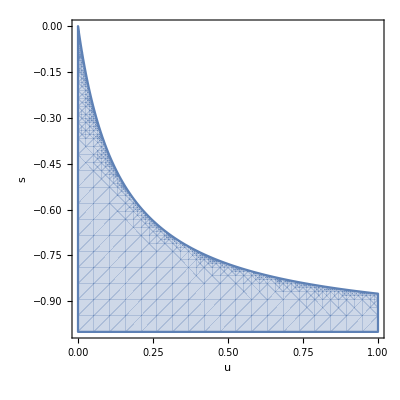

```mathematica
RegionPlot[stab8,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
k̄[7]/.sol[[8]]//Simplify
```

-(49 u)/(s+7 s u)

```mathematica
𝒱[7]/.sol[[8]]//Simplify
```

-(49 u (s+7 u+7 s u))/(s+7 s u)^2

```mathematica
𝒮[7]/.sol[[8]]//Simplify
```

-(49 u (98 u^2+21 s u (1+7 u)+(s+7 s u)^2))/(s+7 s u)^3

At this point Solve has trouble finding solutions.  The following confirms the general form of the solutions from n = 8 to 50.

### n=8

```mathematica
nextf=f[8]+delta[8,s,u];
```

```mathematica
sol=eq[8,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,8}]//Simplify
```

{True,True,True,True,True,True,True,True}

```mathematica
jac=Table[Table[D[nextf[[i]],Subscript[f, j]],{j,0,7}],{i,1,8}]//Simplify;
```

```mathematica
jac8=jac/.sol//Simplify;
```

```mathematica
eig8=Eigenvalues[jac8]//Simplify
```

{(1+s) (1+8 u),1/2 (2+s+8 u+8 s u),1/4 (4+s+8 u+8 s u),1+6 u+s (3/4+6 u),1+3 u+s (3/8+3 u),1+5 u+s (5/8+5 u),1+7 u+s (7/8+7 u),1+u+8 u^2+1/8 s (1+8 u)^2}

```mathematica
stab8=Reduce[Flatten[{Table[-1<eig8[[i]]<1,{i,1,8}],0<u<1,-1<s<0}]]
```

0<u<1&&-1<s<-(8 u)/(1+8 u)

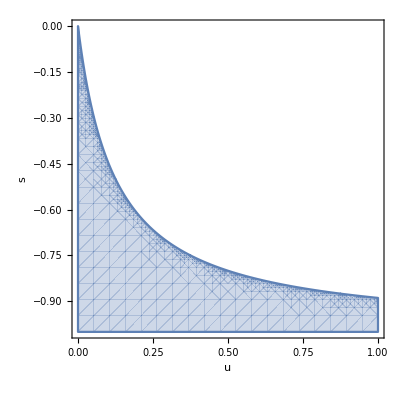

```mathematica
RegionPlot[stab8,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

### n=9

```mathematica
nextf=f[9]+delta[9,s,u];
```

```mathematica
sol=eq[9,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,9}]//Simplify
```

{True,True,True,True,True,True,True,True,True}

### n=10

```mathematica
nextf=f[10]+delta[10,s,u];
```

```mathematica
sol=eq[10,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,10}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True}

### n=11

```mathematica
nextf=f[11]+delta[11,s,u];
```

```mathematica
sol=eq[11,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,11}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True}

### n=12

```mathematica
nextf=f[12]+delta[12,s,u];
```

```mathematica
sol=eq[12,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,12}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True}

### n=13

```mathematica
nextf=f[13]+delta[13,s,u];
```

```mathematica
sol=eq[13,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,13}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=14

```mathematica
nextf=f[14]+delta[14,s,u];
```

```mathematica
sol=eq[14,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,14}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=15

```mathematica
nextf=f[15]+delta[15,s,u];
```

```mathematica
sol=eq[15,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,15}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=16

```mathematica
nextf=f[16]+delta[16,s,u];
```

```mathematica
sol=eq[16,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,16}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=17

```mathematica
nextf=f[17]+delta[17,s,u];
```

```mathematica
sol=eq[17,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,17}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=18

```mathematica
nextf=f[18]+delta[18,s,u];
```

```mathematica
sol=eq[18,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,18}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=19

```mathematica
nextf=f[19]+delta[19,s,u];
```

```mathematica
sol=eq[19,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,19}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=20

```mathematica
nextf=f[20]+delta[20,s,u];
```

```mathematica
sol=eq[20,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,20}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=21

```mathematica
nextf=f[21]+delta[21,s,u];
```

```mathematica
sol=eq[21,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,21}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=22

```mathematica
nextf=f[22]+delta[22,s,u];
```

```mathematica
sol=eq[22,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,22}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=23

```mathematica
nextf=f[23]+delta[23,s,u];
```

```mathematica
sol=eq[23,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,23}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=24

```mathematica
nextf=f[24]+delta[24,s,u];
```

```mathematica
sol=eq[24,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,24}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=25

```mathematica
nextf=f[25]+delta[25,s,u];
```

```mathematica
sol=eq[25,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,25}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=26

```mathematica
nextf=f[26]+delta[26,s,u];
```

```mathematica
sol=eq[26,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,26}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=27

```mathematica
nextf=f[27]+delta[27,s,u];
```

```mathematica
sol=eq[27,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,27}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=28

```mathematica
nextf=f[28]+delta[28,s,u];
```

```mathematica
sol=eq[28,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,28}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=29

```mathematica
nextf=f[29]+delta[29,s,u];
```

```mathematica
sol=eq[29,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,29}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=30

```mathematica
nextf=f[30]+delta[30,s,u];
```

```mathematica
sol=eq[30,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,30}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=31

```mathematica
nextf=f[31]+delta[31,s,u];
```

```mathematica
sol=eq[31,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,31}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=32

```mathematica
nextf=f[32]+delta[32,s,u];
```

```mathematica
sol=eq[32,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,32}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=33

```mathematica
nextf=f[33]+delta[33,s,u];
```

```mathematica
sol=eq[33,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,33}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=34

```mathematica
nextf=f[34]+delta[34,s,u];
```

```mathematica
sol=eq[34,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,34}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=35

```mathematica
nextf=f[35]+delta[35,s,u];
```

```mathematica
sol=eq[35,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,35}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=36

```mathematica
nextf=f[36]+delta[36,s,u];
```

```mathematica
sol=eq[36,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,36}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=37

```mathematica
nextf=f[37]+delta[37,s,u];
```

```mathematica
sol=eq[37,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,37}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=38

```mathematica
nextf=f[38]+delta[38,s,u];
```

```mathematica
sol=eq[38,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,38}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=39

```mathematica
nextf=f[39]+delta[39,s,u];
```

```mathematica
sol=eq[39,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,39}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=40

```mathematica
nextf=f[40]+delta[40,s,u];
```

```mathematica
sol=eq[40,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,40}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=41

```mathematica
nextf=f[41]+delta[41,s,u];
```

```mathematica
sol=eq[41,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,41}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=42

```mathematica
nextf=f[42]+delta[42,s,u];
```

```mathematica
sol=eq[42,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,42}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=43

```mathematica
nextf=f[43]+delta[43,s,u];
```

```mathematica
sol=eq[43,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,43}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=44

```mathematica
nextf=f[44]+delta[44,s,u];
```

```mathematica
sol=eq[44,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,44}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=45

```mathematica
nextf=f[45]+delta[45,s,u];
```

```mathematica
sol=eq[45,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,45}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=46

```mathematica
nextf=f[46]+delta[46,s,u];
```

```mathematica
sol=eq[46,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,46}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=47

```mathematica
nextf=f[47]+delta[47,s,u];
```

```mathematica
sol=eq[47,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,47}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=48

```mathematica
nextf=f[48]+delta[48,s,u];
```

```mathematica
sol=eq[48,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,48}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=49

```mathematica
nextf=f[49]+delta[49,s,u];
```

```mathematica
sol=eq[49,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,49}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### n=50

```mathematica
nextf=f[50]+delta[50,s,u];
```

```mathematica
sol=eq[50,s,u];
```

```mathematica
subs=nextf/.sol//Simplify;
```

```mathematica
Table[Values[sol[[i]]]==subs[[i]],{i,1,50}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}